# Supplementary Information for Quantitatively Visualizing Bipartite Datasets

The following code reproduces the plots in the main text. Made on Mathematica version 13.2.0 for Windows. Sections can be opened by mouse click.

Raw data can be found in the initialization section.

## Figures

### Figure 1: Overview of MDS

We compare the classic localization problem (where distance can be measured between any pair of entries) with bipartite localization (where distance can only be measured between, and not within, two classes of entries).

#### Panel A: Color-Color Distance

An example of classic localization using the canonical color wheel example. We apply metric MDS to previously published data.

```mathematica
(* Table 4.1 (page 65) of Modern MDShttps://www.google.com/books/edition/Modern_Multidimensional_Scaling/duTODldZzRcC?hl=en&gbpv=1Nonehttps://www.google.com/books/edition/Modern_Multidimensional_Scaling/duTODldZzRcC?hl=en&gbpv=1HyperlinkActionRecycledHyperlinkActive by Borg & Groenen *)
distRaw={{0},{0.86,0},{0.42,0.50,0},{0.42,0.44,0.81,0},{0.18,0.22,0.47,0.54,0},{0.06,0.09,0.17,0.25,0.61,0},{0.07,0.07,0.10,0.10,0.31,0.62,0},{0.04,0.07,0.08,0.09,0.26,0.45,0.73,0},{0.02,0.02,0.02,0.02,0.07,0.14,0.22,0.33,0},{0.07,0.04,0.01,0.01,0.02,0.08,0.14,0.19,0.58,0},{0.09,0.07,0.02,0.00,0.02,0.02,0.05,0.04,0.37,0.74,0},{0.12,0.11,0.01,0.01,0.01,0.02,0.02,0.03,0.27,0.50,0.76,0},{0.13,0.13,0.05,0.02,0.02,0.02,0.02,0.02,0.20,0.41,0.62,0.85,0},{0.16,0.14,0.03,0.04,0.00,0.01,0.00,0.02,0.23,0.28,0.55,0.68,0.76,0}};
distMatrix=PadRight[#,Length@distRaw]&/@distRaw;
distMatrix=distMatrix+Transpose@distMatrix+IdentityMatrix[Length@distMatrix];
(* Transform from dissimilarity to similarity *)
distMatrix=1-distMatrix;
```

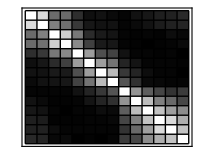

```mathematica
wavelengthsColors=ColorData["VisibleSpectrum"]/@{434,445,465,472,490,504,537,555,584,600,610,628,651,674};
ArrayPlot[distMatrix,PlotRangePadding->None,ImageSize->200,Frame->True,Mesh->True,MeshStyle->Directive[Black,Thin],FrameTicks->{MapIndexed[{First@#2,Row[{Graphics[{#,EdgeForm[Directive[Thickness[Small],Black]],Disk[]},ImageSize->9]}]}&,wavelengthsColors],None,None,MapIndexed[{First@#2,Row[{Graphics[{#,EdgeForm[Directive[Thickness[Small],Black]],Disk[]},ImageSize->9]}]}&,wavelengthsColors]},AspectRatio->0.8,ColorFunctionScaling->False]
BarLegend[{GrayLevel[1-#]&,{0,1}},LegendLayout->"Row",LabelStyle->{FontSize->18},FrameStyle->Directive[Thin,Black]]
```

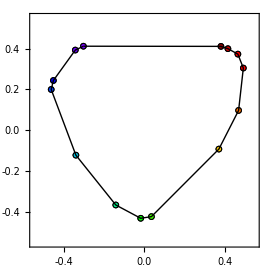

```mathematica
coordsSDP=sdp[distMatrix];
coordsSDP={0.04,0.1}+{-1,1}RotationTransform[2.78][#]&/@coordsSDP;
plotColors=ListPlot[List/@coordsSDP,Frame->{True,True,False,False},FrameTicks->ConstantArray[,2],Axes->False,PlotMarkers->plotMarker[0.065,"EdgeThickness"->Medium],PlotStyle->wavelengthsColors,PlotRange->ConstantArray[0.55{-1,1},2],AspectRatio->1,ImageSize->270,Epilog->{Thick,Line[coordsSDP,VertexColors->wavelengthsColors],Line[{coordsSDP[[-1]],coordsSDP[[1]]},VertexColors->wavelengthsColors[[{-1,1}]]]},FrameTicksStyle->16]
```

#### Panel B: Schematic of Antibody-Virus Distance

Below we draw some schematic antibody-virus data to explain the benefits of embedding this bipartite data.

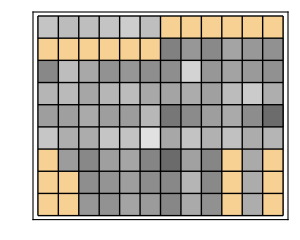

```mathematica
ArrayPlot[,PlotRangePadding->None,ImageSize->300,ColorFunctionScaling->False,Frame->True,Mesh->True,MeshStyle->Directive[Black,Thin],ColorRules->{_Missing->colorMissing,val_Real:>GrayLevel[1-Rescale[val,MinMax@DeleteCases[Flatten@plotData,_Missing]]]},FrameTicks->{MapIndexed[{First@#2,Row[{Graphics[{colorAbInMixture,markerAb["Thickness"->0.01][[1,1]]},ImageSize->20]}]}&,Range@9],None,None,MapIndexed[{First@#2,Column[{Graphics[{#,markerVirus["Opacity"->1,"OpacityFaceFormFactor"->1][[1,1]]},ImageSize->22]},Alignment->Center]}&,{RGBColor[0.7652173913043478, 0.9721739130434782, 0.7652173913043478],RGBColor[0.7304347826086957, 0.9443478260869566, 0.7304347826086957],RGBColor[0.6956521739130435, 0.9165217391304348, 0.6956521739130435],RGBColor[0.6260869565217392, 0.8608695652173913, 0.6260869565217392],RGBColor[0.5565217391304348, 0.8052173913043478, 0.5565217391304348],RGBColor[0.48695652173913045, 0.7495652173913043, 0.48695652173913045],RGBColor[0.4173913043478261, 0.6939130434782608, 0.4173913043478261],RGBColor[0.3478260869565218, 0.6382608695652174, 0.3478260869565218],RGBColor[0.27826086956521745, 0.5826086956521739, 0.27826086956521745],RGBColor[0.20869565217391306, 0.5269565217391304, 0.20869565217391306],RGBColor[0.10434782608695659, 0.4434782608695652, 0.10434782608695659],RGBColor[0.06956521739130439, 0.41565217391304354, 0.06956521739130439]}]},AspectRatio->0.8]
```

Note: The right panel in Figure 1b was only a schematic

### Figure 2: Phase Diagram of Synthetic Data

Comparison of metric MDS, bipartite MDS, and SDP at different noise levels and fractions of missing values.

For speed, the values for the phase diagrams are canned in the initialization section

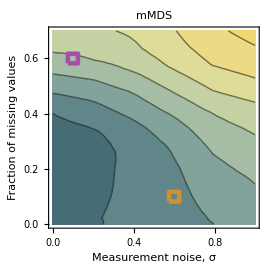
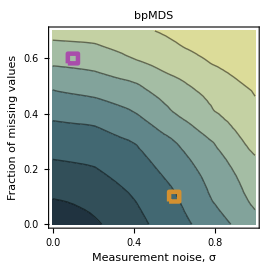
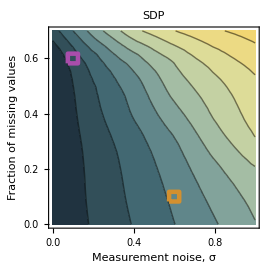
-Graphics- |  | -Graphics- |  | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
methods={"mMDS","cMDS","SDP"};
legPhaseDigrams=BarLegend[{ColorData["StarryNightColors"],{0,1}},LegendMarkerSize->200,Ticks->({#,If[MemberQ[Range[0,1,0.2],#],format[#,1],""]}&/@Range[0,1,0.1]),LabelStyle->14];
legExamplePlots=PointLegend[ColorData[95]/@{1,2,1,2},font/@{"Virus (Ground Truth)","Virus (Numerical)","Antibody (Ground Truth)","Antibody (Numerical)"},LegendMarkers->{plotMarker[0.05],plotMarker[0.7 0.05],plotMarker[1.125 0.05,"Type"->"Square"],plotMarker[0.7 1.125 0.05,"Type"->"Square"]},LegendFunction->frame];
Grid[{Append[Riffle[Table[drawPhaseDiagram[dataPhaseDiagram,method,MaxPlotPoints->25,InterpolationOrder->1],{method,methods}],SpanFromLeft,{2,-1,2}],legPhaseDigrams],Append[Flatten[drawExamplePlots/@methods],legExamplePlots]},Spacings->{2,2},Alignment->{Left}]
```

### Figure 3: Outliers

Analyzing how the embedding algorithms perform with several large outliers.

```mathematica
{nVirus,nAb}={10,12};
outliers={{1,1},{2,2},{3,1}}->10;
lowerBounds={{6,8},{2,7},{9,5},{8,5},{7,7},{8,6},{6,2},{7,10},{4,2},{4,9},{5,3},{6,9},{1,2},{8,1},{9,8},{7,12},{4,5},{9,11}};
upperBounds={{8,11},{8,4},{3,9},{4,10},{4,8},{9,9},{7,3},{8,7},{2,1},{4,12},{1,6},{6,5},{2,3},{3,5},{10,1},{1,10},{10,8},{5,7}};
plotMarkerSize=12;
```

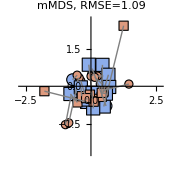
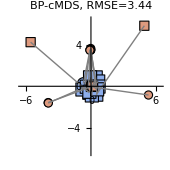
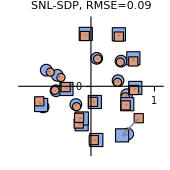
X^*
(-0.76, -0.34)
(0.57, -0.14)
(-0.55, -0.07)
(0.48, 0.42)
(0.58, -0.79)
(-0.24, -0.30)
(0.09, 0.46)
(0.43, 0.09)
(-0.53, 0.18)
(-0.71, 0.27) | Y^*
(0.49, -0.81)
(-0.15, -0.63)
(0.44, 0.86)
(-0.79, -0.31)
(0.67, 0.46)
(-0.08, 0.86)
(-0.39, -0.04)
(0.06, -0.26)
(0.09, -0.89)
(-0.14, -0.53)
(0.70, -0.03)
(0.57, -0.30) | (1.34→10 | 0.67 | 1.70 | 0.04 | 1.64 | 1.38 | 0.47 | 0.82 | 1.00 | 0.64 | 1.49 | 1.33
0.68 | 0.86→10 | 1.01 | 1.36 | 0.61 | 1.20 | 0.96 | 0.52 | 0.89 | 0.81 | 0.18 | 0.16
1.28→10 | 0.69 | 1.36 | 0.33 | 1.34 | 1.05 | 0.17 | 0.64 | 1.03 | 0.61 | 1.26 | 1.15
1.23 | 1.21 | 0.44 | 1.46 | 0.20 | 0.72 | 0.98 | 0.79 | 1.36 | 1.13 | 0.50 | 0.72
0.09 | 0.75 | 1.65 | 1.45 | 1.25 | 1.78 | 1.22 | 0.74 | 0.51 | 0.77 | 0.77 | 0.49
0.89 | 0.34 | 1.35 | 0.55 | 1.19 | 1.18 | 0.30 | 0.30 | 0.67 | 0.25 | 0.98 | 0.81
1.33 | 1.11 | 0.53 | 1.17 | 0.58 | 0.44 | 0.70 | 0.72 | 1.35 | 1.02 | 0.78 | 0.90
0.91 | 0.92 | 0.77 | 1.28 | 0.44 | 0.93 | 0.83 | 0.51 | 1.04 | 0.85 | 0.30 | 0.42
1.43 | 0.90 | 1.19 | 0.55 | 1.24 | 0.82 | 0.27 | 0.74 | 1.23 | 0.81 | 1.25 | 1.21
1.61 | 1.05 | 1.29 | 0.58 | 1.39 | 0.87 | 0.45 | 0.93 | 1.40 | 0.98 | 1.44 | 1.40)True Distance Matrix D^* → Corrupted Matrix D with Large Outliers |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
{coords,distMatrix}=exampleData[{nVirus,nAb},0.];
distMatrixOutliers=ReplacePart[distMatrix,outliers];
(* Show distance matrix corrupted with large outliers *)
{showVirusCoords,showAbCoords,showDistMatrixOutliers}={showGrid[List/@Prepend[font@Row[{"(",format[#[[1]],2],", ",format[#[[2]],2],")"}]&/@First@coords,"X^*"]],showGrid[List/@Prepend[font@Row[{"(",format[#[[1]],2],", ",format[#[[2]],2],")"}]&/@Last@coords,"Y^*"]],MatrixForm[MapAt[Item[#->font[Last@outliers,Bold,Darker@Red],Background->LightRed]&,Map[font@format[#,2]&,distMatrix,{2}],First@outliers]]};
(* cMDS and SDP on outlier data *)
{resSDP,resClassicalMDS,resMetricMDS}=Quiet@{
coordsMDS=sdp[distMatrixOutliers];
Show[analyzeMDS[coords,coordsMDS,LegendLabel->"SDP","AddToPlotLabel"->Row[{Style["SNL-SDP",Bold],", "}],"PlotLabelSize"->15,"ShowLegend"->False,"ConnectNumericToActual"->True,"Comparing"->"Distance","PenalizeError"->"RMSE","ErrorLabel"->"RMSE",PlotRange->1.1{-1,1},PlotStyle->colorsEmbedding,"PlotMarkerSize"->plotMarkerSize],Ticks->ConstantArray[,2]],
coordsMDS=classicalMDS[distMatrixOutliers];
analyzeMDS[coords,coordsMDS,"AddToPlotLabel"->Row[{Style["BP-cMDS",Bold],", "}],"PlotLabelSize"->15,"ShowLegend"->False,"ConnectNumericToActual"->True,"Comparing"->"Distance","PenalizeError"->"RMSE","ErrorLabel"->"RMSE",PlotStyle->colorsEmbedding,"PlotMarkerSize"->plotMarkerSize],
coordsMDS=metricMDS[distMatrixOutliers,"SearchMethod"->Automatic,"SearchPoints"->Automatic,"Comparing"->"Distance","PenalizeError"->"MeanSquaredError"];
analyzeMDS[coords,coordsMDS,LegendLabel->"mMDS","AddToPlotLabel"->Row[{Style["mMDS",Bold],", "}],"PlotLabelSize"->15,"ConnectNumericToActual"->True,"Comparing"->"Distance","PenalizeError"->"RMSE","ErrorLabel"->"RMSE",PlotStyle->colorsEmbedding,"ShowLegend"->False,"PlotMarkerSize"->plotMarkerSize]};
gridOutliers=Grid[{{Grid[{{showVirusCoords,showAbCoords,Labeled[showDistMatrixOutliers,showGrid[{{"True Distance Matrix D^* → Corrupted Matrix D with Large Outliers"}}],Top]}},Spacings->2,Alignment->Top],SpanFromLeft},{resMetricMDS,resClassicalMDS,resSDP}},Spacings->{2,2}]
```

Embedding data that contains upper and lower bounds

```mathematica
(* === Modify data to include upper/lower bounds === *)
SeedRandom[12345];
distMatrixBounds=distMatrix;
Do[
distMatrixBounds[[Sequence@@bound]]=LessThan[distMatrixBounds[[Sequence@@bound]]+RandomReal[{0.1,0.5}]]
,{bound,lowerBounds}];
Do[
distMatrixBounds[[Sequence@@bound]]=GreaterThan[Max[distMatrixBounds[[Sequence@@bound]]-RandomReal[{0.1,0.5}],0]]
,{bound,upperBounds}];
showDistMatrixBounds=MatrixForm[MapAt[Item[#,Background->LightPurple]&,MapAt[Item[#,Background->LightBlue]&,Map[font@format[#,2]&,distMatrixBounds,{2}],upperBounds],lowerBounds]];
```

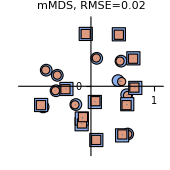
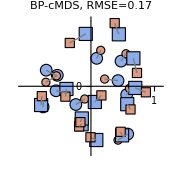
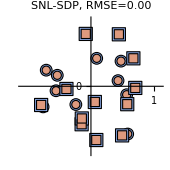
(1.34 | <0.99 | 1.70 | 0.04 | 1.64 | >0.95 | 0.47 | 0.82 | 1.00 | >0.35 | 1.49 | 1.33
>0.53 | 0.86 | >0.72 | 1.36 | 0.61 | 1.20 | <1.19 | 0.52 | 0.89 | 0.81 | 0.18 | 0.16
1.28 | 0.69 | 1.36 | 0.33 | >0.86 | 1.05 | 0.17 | 0.64 | >0.64 | 0.61 | 1.26 | 1.15
1.23 | <1.63 | 0.44 | 1.46 | <0.39 | 0.72 | 0.98 | >0.52 | <1.50 | >0.99 | 0.50 | >0.48
0.09 | 0.75 | <1.91 | 1.45 | 1.25 | 1.78 | >0.97 | 0.74 | 0.51 | 0.77 | 0.77 | 0.49
0.89 | <0.73 | 1.35 | 0.55 | >0.80 | 1.18 | 0.30 | <0.45 | <0.91 | 0.25 | 0.98 | 0.81
1.33 | 1.11 | >0.14 | 1.17 | 0.58 | 0.44 | <0.89 | 0.72 | 1.35 | <1.40 | 0.78 | <1.22
<1.30 | 0.92 | 0.77 | >0.93 | <0.71 | <1.21 | >0.36 | 0.51 | 1.04 | 0.85 | >0.14 | 0.42
1.43 | 0.90 | 1.19 | 0.55 | <1.65 | 0.82 | 0.27 | <1.13 | >1.06 | 0.81 | <1.59 | 1.21
>1.39 | 1.05 | 1.29 | 0.58 | 1.39 | 0.87 | 0.45 | >0.62 | 1.40 | 0.98 | 1.44 | 1.40)D^* → D with Upper/Lower Bounds |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
{resSDPbounds,resClassicalMDSbounds,resMetricMDSbounds}={
coordsSDP=sdp[distMatrixBounds];
Show[analyzeMDS[coords,coordsSDP,LegendLabel->"SDP","AddToPlotLabel"->Row[{Style["SNL-SDP",Bold],", "}],"PlotLabelSize"->15,"AddToPlotLabel"->"SDP, ","ShowLegend"->False,"ConnectNumericToActual"->True,"Comparing"->"Distance","PenalizeError"->"RMSE","ErrorLabel"->"RMSE",PlotRange->1.1{-1,1},PlotStyle->colorsEmbedding,"PlotMarkerSize"->plotMarkerSize],Ticks->ConstantArray[,2]],
coordsMDS=classicalMDS[distMatrixBounds];
Show[analyzeMDS[coords,coordsMDS,"AddToPlotLabel"->Row[{Style["BP-cMDS",Bold],", "}],"PlotLabelSize"->15,"ShowLegend"->False,"ConnectNumericToActual"->True,"Comparing"->"Distance","PenalizeError"->"RMSE","ErrorLabel"->"RMSE",PlotRange->1.1{-1,1},PlotStyle->colorsEmbedding,"PlotMarkerSize"->plotMarkerSize],Ticks->ConstantArray[,2]],
coordsmMDS=metricMDS[distMatrixBounds,"SearchMethod"->Automatic,"SearchPoints"->Automatic,"Comparing"->"Distance","PenalizeError"->"MeanSquaredError"];
Show[analyzeMDS[coords,coordsmMDS,LegendLabel->"mMDS","AddToPlotLabel"->Row[{Style["mMDS",Bold],", "}],"PlotLabelSize"->15,"AddToPlotLabel"->"SDP, ","ConnectNumericToActual"->True,"Comparing"->"Distance","PenalizeError"->"RMSE","ErrorLabel"->"RMSE",PlotStyle->colorsEmbedding,"ShowLegend"->False(*,"OverrideLabel"->{"X^*","X","Y^*","Y"}*),PlotRange->1.1{-1,1},"PlotMarkerSize"->plotMarkerSize],Ticks->ConstantArray[,2]]};
gridBounds=Grid[{{Labeled[showDistMatrixBounds,showGrid[{{"D^* → D with Upper/Lower Bounds"}}],Top],SpanFromLeft,SpanFromLeft},{resMetricMDSbounds,resClassicalMDSbounds,resSDPbounds}},Spacings->{2,2}]
```

### Figure 4: Antibody-Virus Data

Here, we assess the embedding algorithms using antibody-virus neutralization data from Creanga 2021, with the raw data provided in the initialization section.

#### Visualizing the Ab-Virus Data

We transform the concentration of antibodies necessary to neutralize 50% of viruses (IC_50 in Molar units) into map distance using dist=Log10[IC_50/(10^-10 M)].

```mathematica
distMatrix=neutralizationData[[All,All,3]]/.val_Real:>Log10[val/10^-10];
posGreaterThan=Position[distMatrix,_GreaterThan,Heads->False];
posMissing=Position[distMatrix,_Missing,Heads->False];
dataAbVirusMatrix=MapAt[Item["-",Background->colorMissing]&,MapAt[Item[Row[{font[">"],#[[1]]}],Background->colorGreaterThan]&,distMatrix/.val_Real:>font[Round[val,0.1]],posGreaterThan],posMissing];
Grid[Prepend[Transpose@Prepend[dataAbVirusMatrix,MapIndexed[Graphics[{plotStyleVirus@#,markerVirus["Opacity"->1,"OpacityFaceFormFactor"->1][[1,1]]},ImageSize->20]&,orderedVirus]],Prepend[ConstantArray[Graphics[{colorAbInMixture,markerAb["Thickness"->0.01][[1,1]]},ImageSize->20],First@Dimensions@dataAbVirusMatrix],""]]]
```

| -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | >3.2 | >3.2 | 2.4 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 0.9 | 2.8 | 1.8 | 1. | 2.7 | 2.4 | 0.5 | 1. | -0.1 | 0.3 | 0.3 | 0.5 | 0.4 | 0. | 0.6 | 0.7 | -0.1 | 0.8 | 0.5
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | - | - | >3.2 | - | >3.2 | >3.2 | - | - | - | - | 2.3 | 2. | 0.7 | 1.2 | 1.3 | 1.4 | 1.5 | 0.9 | - | - | 0.7 | - | 1.5
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | - | - | >3.2 | - | >3.2 | >3.2 | - | - | - | - | 1.4 | 1.2 | 1. | 1.2 | 1.3 | 1. | 0.8 | 0.8 | - | 1.2 | 0.8 | - | 1.1
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 3.2 | 1.8 | 2.7 | 2.7 | 2. | 1.7 | 1. | 1. | 1.1 | 0.9 | 1.1 | 1.1 | 1.3 | 1.5 | 0.8 | 1.4 | 0.8
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | - | - | >3.2 | - | >3.2 | >3.2 | - | - | - | - | 2.7 | 2.4 | 0.6 | 1.4 | 1.7 | 1.5 | 1.5 | 1. | - | - | 0.9 | - | 1.1
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.2 | 2.7 | >3.2 | >3.2 | 1.9 | 2.2 | 0.7 | 1.2 | 1.5 | 1.6 | 1.3 | 0.9 | 1.3 | 1.2 | 0.7 | 1.3 | 1.1
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.9 | 1.9 | 2.4 | 1.4 | >3.2 | 2.3 | 1.6 | 1.8 | 0.5 | 1.1 | 0.8 | 1.2 | 1. | 0.7 | 0.8 | 0.8 | 0.7 | 0.9 | 1.
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.8 | 1.5 | 3.1 | 2.3 | 2. | 2. | 0.7 | 1.2 | 1.1 | 1.3 | 1.3 | 0.8 | 1.1 | 1.1 | 0.6 | 1.2 | 1.2
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.7 | >3.2 | 1.9 | >3.2 | 2.7 | 2. | 1.7 | 0.7 | 1. | 1. | 1.2 | 0.9 | 0.9 | 1.3 | 1.5 | 0.8 | 1.5 | 1.
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2. | 2.5 | 2.4 | 2.2 | 2.1 | 0.3 | 0.9 | 1.1 | 1.4 | 1.4 | 1.1 | 1.2 | 1.5 | 0.8 | 1.4 | 1.1
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.3 | >3.2 | >3.2 | 2.8 | 2.9 | 1. | 1.5 | 2.2 | 2.2 | 1.3 | 1.4 | 1.5 | 1.7 | 1. | 1.6 | 1.5
-Graphics- | >3.2 | >3.2 | 2.7 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.1 | 1.9 | >3.2 | 1.7 | >3.2 | >3.2 | 2.3 | 1.6 | 1.1 | 1.7 | 1.7 | 1.6 | 1.4 | 1.1 | 1.5 | 1.8 | 1.3 | 1.5 | 1.7
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | - | - | >3.2 | - | 1.6 | 1.5 | - | - | - | - | 1.5 | 1.7 | 0.6 | 1. | 1.1 | 1.1 | 0.9 | 0.9 | - | - | 0.8 | - | 1.2
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.2 | 1.6 | >3.2 | 1.5 | >3.2 | 2.5 | 1.6 | 1.4 | 0.7 | 1.4 | 1.3 | 1.3 | 0.5 | 1. | 1. | 1.1 | 1. | 0.9 | 1.3
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | - | - | >3.2 | - | >3.2 | >3.2 | - | - | - | - | >3.2 | 2.5 | 0.8 | 1.4 | 1.6 | 1.6 | 1.3 | 0.9 | 1.5 | - | 1.1 | - | 1.4
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.3 | 1.9 | >3.2 | >3.2 | 3.2 | 2.3 | 0.9 | 1.2 | 1.4 | 1.5 | 1.3 | 1.2 | 1.3 | 1.5 | 1. | 1.5 | 1.6
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.3 | >3.2 | >3.2 | >3.2 | 3.2 | 1.3 | 1.6 | 1.8 | 2. | 1.9 | 1.4 | 1.2 | 1.6 | 1.4 | 1.4 | 1.2
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | - | - | >3.2 | - | >3.2 | 2.9 | - | - | - | - | 2.3 | 2. | 0.7 | 1. | 1.1 | 1.1 | 1.1 | 0.8 | - | - | 0.7 | - | 1.4
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | - | - | >3.2 | - | >3.2 | >3.2 | - | - | - | - | 2.6 | 2.1 | 0.4 | 0.6 | 1.1 | 0.8 | 0.7 | 0.3 | 0.8 | - | 0.5 | - | 0.6
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2. | >3.2 | >3.2 | >3.2 | 2.8 | 1.1 | 1.3 | 1.2 | 1.7 | 1.6 | 0.9 | 1. | 1. | 0.9 | 1.2 | 1.
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2. | 2.2 | 2.7 | 1.6 | 1.4 | >3.2 | >3.2 | 1.8 | 1.7 | 1.4 | 1. | 1.4 | 0.8 | 1.3 | 1.2 | 0.6 | 1. | 1. | 1.2 | 1. | 1.5
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | - | - | 2.2 | - | >3.2 | 2.6 | - | - | - | - | 2.1 | 1.6 | 0.9 | 1.8 | 1.7 | 1.4 | 1.4 | 1. | - | - | 1.4 | - | 1.3
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.2 | 2.1 | >3.2 | 2.6 | 1.7 | >3.2 | >3.2 | 2.2 | 2.2 | 1.7 | 1.2 | 1.9 | 1.8 | 1.8 | 1.5 | 1. | 1.4 | 1.4 | 1.4 | 1.3 | 1.4
-Graphics- | 1.6 | 1.4 | 1.1 | 1.7 | 2.2 | 2.8 | 1.8 | 2.2 | 1.3 | 1.3 | 2.1 | 1.8 | >3.2 | 3. | 1.9 | >3.2 | 1.3 | 1.7 | 1.5 | 2.1 | 2. | 2.5 | 2.1 | >3.2 | >3.2 | >3.2 | >3.2
-Graphics- | 1.3 | 0.9 | 1. | 1.4 | - | - | 1.7 | - | 0.7 | 1.2 | - | - | - | - | 1.3 | 2.6 | 1.3 | 1.3 | 1.2 | 1.6 | 2.1 | 2.3 | - | - | >3.2 | - | >3.2
-Graphics- | 1.3 | 0.7 | 0.8 | 1.2 | 1.1 | 1.6 | 1.5 | 1. | 0.7 | 0.9 | 1.1 | 0.9 | 2.2 | 1.6 | 1.2 | 2.3 | 1.3 | 1.3 | 1.2 | 1.4 | 1.6 | 2.4 | 1.1 | >3.2 | >3.2 | >3.2 | >3.2
-Graphics- | 1.4 | 0.6 | 0.6 | 1. | 1.8 | 2.4 | 1.3 | 1.7 | 0.3 | 0.7 | 1.8 | 1.4 | 2.3 | 2.5 | 1.1 | 2.1 | 1.4 | 1.1 | 0.9 | 1.3 | 2.1 | 1.9 | 2. | >3.2 | >3.2 | >3.2 | >3.2
-Graphics- | 1.3 | 0.9 | 0.9 | 1.5 | - | - | 1.5 | - | 0.5 | 1.4 | - | - | - | - | 1.7 | 2.8 | 1.4 | 1.3 | 1.5 | 1.9 | 2.2 | 2.4 | - | - | >3.2 | - | >3.2
-Graphics- | 1.6 | 1.1 | 0.9 | 1.4 | - | - | 1.5 | - | 0.9 | 1. | - | - | - | - | 1.7 | 2.5 | 1.2 | 1.4 | 1.4 | 1.5 | 1.6 | 2.6 | - | - | >3.2 | - | >3.2
-Graphics- | 1.4 | 0.7 | 0.5 | 0.8 | 0.7 | 0.8 | 1. | 0.3 | 0.4 | 0.9 | 0.5 | 0.1 | 2.3 | 0.9 | 1.4 | 2.3 | 1. | 1.6 | 1.2 | 1.3 | 1.6 | 1.3 | 1.4 | 1.9 | >3.2 | >3.2 | >3.2
-Graphics- | 1.5 | 1. | 1. | 1.3 | - | - | 1.5 | - | 0.9 | 1.1 | - | - | - | - | 1.6 | 2.6 | 1.5 | 1.5 | 1.4 | 1.5 | 1.8 | 2.2 | - | - | >3.2 | - | >3.2
-Graphics- | 1.3 | 1.2 | 0.9 | 1.2 | - | - | 1.2 | - | 0.8 | 1.1 | - | - | 2.5 | 2.3 | 1.6 | 2.5 | 1.2 | 1.5 | 1.6 | 1.5 | 1.7 | 1.8 | >3.2 | - | >3.2 | - | >3.2
-Graphics- | 1.5 | 0.9 | 0.9 | 1.3 | - | - | 1.5 | - | 0.8 | 1.3 | - | - | - | - | 1.7 | 3. | 1.5 | 1.6 | 1.7 | 1.8 | 2.2 | 2.2 | - | - | >3.2 | - | >3.2
-Graphics- | 1.6 | 1.1 | 1.1 | 1.4 | 1.7 | 1.8 | 1.7 | 1.5 | 1. | 1.3 | 1.3 | 1.4 | 2.3 | 2.1 | 1.7 | 2.6 | 1.7 | 1.7 | 1.5 | 1.6 | 2. | 2.3 | 2.3 | >3.2 | >3.2 | >3.2 | >3.2
-Graphics- | 1.3 | 1. | 0.9 | 1.5 | - | - | 1.7 | - | 1. | 0.9 | - | - | - | - | 1.8 | 2.8 | 1.8 | 1.5 | 1.4 | 1.8 | 2.1 | 2.6 | - | - | >3.2 | - | >3.2
-Graphics- | 1. | 0.8 | 0.7 | 0.8 | 0.7 | 0.9 | 0.7 | 0.6 | 0.5 | 0.7 | 0.4 | 0.1 | 1.2 | 0.8 | >3.2 | 2.1 | 0.6 | 1. | 1. | 0.8 | 1.3 | 1.5 | 2.1 | 2.6 | >3.2 | >3.2 | >3.2
-Graphics- | 1.7 | 1.5 | 1.1 | 1.7 | - | - | 1.5 | - | 1.4 | 1.8 | - | - | - | - | >3.2 | >3.2 | 1.6 | 1.5 | 1.8 | 1.7 | 2.3 | 2.3 | - | - | >3.2 | - | >3.2
-Graphics- | 1.7 | 1.8 | 1.3 | 1.6 | - | - | 1.6 | - | 1.3 | 1.6 | - | - | - | - | >3.2 | >3.2 | 1.4 | 2. | >3.2 | >3.2 | 1.6 | 2.7 | - | - | >3.2 | - | >3.2
-Graphics- | 2.3 | 2. | 1.7 | 2.7 | 3. | 2.9 | 1.7 | 2.1 | >3.2 | 2.4 | 2.2 | 2.3 | 2.6 | 2.8 | >3.2 | >3.2 | 2.2 | 2.2 | 2.5 | 2.4 | 3. | 3.1 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2
-Graphics- | 2.3 | 2. | 1.6 | 2.4 | 3.1 | 2.8 | 1.7 | 2.1 | >3.2 | 2.2 | 2.2 | 2.2 | 2.4 | 2.7 | >3.2 | >3.2 | 2. | 2. | 2.2 | 2.1 | 2.4 | 3. | >3.2 | >3.2 | >3.2 | >3.2 | >3.2
-Graphics- | 2.1 | 1.7 | 1.4 | 2.7 | - | - | 1.8 | - | >3.2 | 2. | - | - | 2.1 | 2.1 | >3.2 | >3.2 | 1.7 | 1.8 | 1.8 | 1.9 | 2.7 | 2.8 | >3.2 | - | >3.2 | - | >3.2
-Graphics- | 2.2 | 1.7 | 1.5 | 2.1 | - | - | 1.9 | - | 1.7 | 1.8 | - | - | - | - | 2.5 | >3.2 | 1.8 | 2. | 2.2 | 2.2 | 2.5 | 2.8 | - | - | >3.2 | - | >3.2
-Graphics- | 1.2 | 1.3 | 0.8 | 1.7 | - | - | 1.4 | - | 1.5 | 1.4 | - | - | - | - | 2. | 2.8 | 1.4 | 1.7 | 1.8 | 1.9 | 1.8 | 2.5 | - | - | >3.2 | - | >3.2
-Graphics- | 1.7 | 2.3 | 2.3 | >3.2 | - | - | 2.5 | - | 2.2 | 2. | - | - | 2.1 | 2.3 | >3.2 | >3.2 | 2.2 | 1.7 | 1.8 | 1.7 | 2.3 | 2.2 | >3.2 | - | >3.2 | - | >3.2
-Graphics- | 1.4 | 1.4 | 1.1 | 1.6 | 1.5 | 1.8 | 1.7 | 1.5 | 1.6 | 1.4 | 1. | 1.2 | 2.5 | 2.1 | 2.1 | 2.8 | 1.5 | 1.8 | 1.9 | 1.9 | 1.9 | 2.3 | >3.2 | 2.3 | >3.2 | >3.2 | >3.2
-Graphics- | 1.5 | 2. | 1.8 | 2.4 | 3. | 3. | 2. | 2.6 | 3. | 2.4 | 2.3 | 2.8 | 3.1 | 2.8 | 2.5 | >3.2 | 2.1 | 1.9 | 2.2 | 2.1 | 2.9 | 3. | >3.2 | >3.2 | >3.2 | >3.2 | >3.2
-Graphics- | 1.6 | 2. | 1.8 | 2.3 | 1.6 | 2.2 | 2. | 1.7 | 2.8 | 2.2 | 1.4 | 1.7 | 2.3 | 1.9 | 2.6 | 3.2 | 1.9 | 2. | 2.1 | 2.2 | 2.6 | 2.4 | 2.9 | 2.1 | >3.2 | >3.2 | >3.2
-Graphics- | 1.2 | 1.5 | 1.2 | 1.7 | 1.5 | 1.7 | 1.6 | 1.2 | 2.1 | 1.5 | 1. | 1.3 | 2. | 1.4 | 1.9 | 2.5 | 1.4 | 1.5 | 1.6 | 1.6 | 1.8 | 2.2 | 2.1 | 1.7 | >3.2 | >3.2 | >3.2
-Graphics- | 1.5 | 1.8 | 1.7 | 2. | - | - | 2. | - | 2.1 | 1.8 | - | - | - | - | 2.2 | >3.2 | 1.4 | 1.7 | 1.7 | 1.9 | 2.3 | 2. | - | - | >3.2 | - | >3.2

#### mMDS Solution

Using metric multidimensional scaling to embed this system into 2D. As described in Figure S3, we remove the five worst viruses and five worst antibodies whose positions cannot be robustly determined.

```mathematica
(* Outlier antibodies/viruses to remove *)
worstAbs={"22-1B08","55-1D06","02-1B02","58-6F03","CR6261"};
worstViruses={"H3N2 A/Moscow/10/1999","H3N2 A/Indiana/10/2011","H3N2 A/Switzerland/9715293/2013","H3N2 A/Hong Kong/4801/2014","H3N2 A/Singapore/INFIMH-160019/2016"};
removing=Join[worstAbs,worstViruses];
(* Distance matrix *)
distMatrix=neutralizationData[[All,All,-1]]/.val_Real:>Log10[val/10^-10.];
distMatrix=Transpose@Delete[Transpose@Delete[distMatrix,Position[orderedAbStem,Alternatives@@removing]],Position[orderedVirus,Alternatives@@removing]];
```

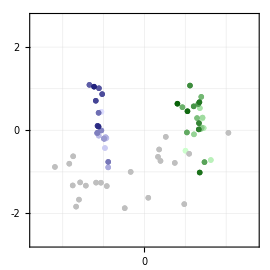

```mathematica
(* For initialization, use landscape coordinates from Einav 2022https://doi.org/10.1038/s43588-022-00375-1

Nonehttps://doi.org/10.1038/s43588-022-00375-1

HyperlinkActionRecycledHyperlinkActive *)
{neutLandscapeCoordsVirus,neutLandscapeCoordsAb}=;
(* mMDS solution *)
coordsMMDS=metricMDS[distMatrix,"SearchMethod"->Automatic,"SearchPoints"->25,"Comparing"->"Distance","PenalizeError"->"MeanSquaredError","InitialPoints"->{neutLandscapeCoordsVirus/@DeleteCases[orderedVirus,Alternatives@@removing],neutLandscapeCoordsAb/@DeleteCases[orderedAbStem,Alternatives@@removing]}];
(* For aesthetic purposes only, we translate and rotate the embedding to match the Einav 2022 embedding which is centered around the origin *)
trans=transform[Join[neutLandscapeCoordsAb/@DeleteCases[orderedAbStem,Alternatives@@removing],neutLandscapeCoordsVirus/@DeleteCases[orderedVirus,Alternatives@@removing]],Join@@coordsMMDS];
(* Match mMDS as closely as possible *)
resMMDS={Association@Thread[DeleteCases[orderedVirus,Alternatives@@removing]->Last@Map[trans,coordsMMDS,{2}]],Association@Thread[DeleteCases[orderedAbStem,Alternatives@@removing]->First@Map[trans,coordsMMDS,{2}]]};
createLandscape[resMMDS,"Tooltip"->True]
```

#### Leave-Some-Out Analysis - Embedding

Comparing embeddings in 1D-4D for the  three embedding algorithms. The results are canned for speed.

```mathematica
methods={"mMDS","cMDS","SDP"};
(*resLeaveSomeOut=runLeaveSomeOut[distMatrix,methods,Range@4,10];
Iconize[resLeaveSomeOut,"Leave some out",Method->Compress]*)
resLeaveSomeOut=;
```

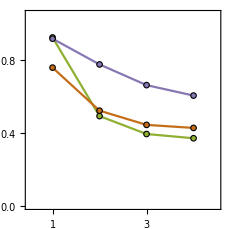

```mathematica
errorDimensions=Table[Table[
plotData=resLeaveSomeOut[{method,dim}];
RootMeanSquare[compare@@@plotData]
,{dim,1,4}],
{method,methods}];
ListPlot[errorDimensions,Joined->True,PlotMarkers->plotMarker[0.045],PlotRange->{{0.5,4.5},{0,1.05}},Frame->{True,True,False,False},FrameTicksStyle->14,PlotStyle->colorsLeaveOneOut,FrameTicks->,AspectRatio->1,ImageSize->230]
```

Showing leave-one-out results (tenfold cross-validation) for 2D embeddings.

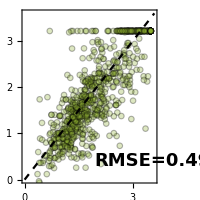
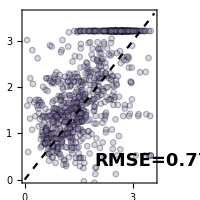
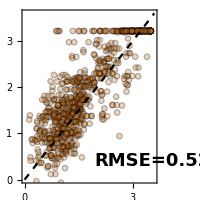

```mathematica
MapIndexed[(
plotData=resLeaveSomeOut[{#,2}];
(* Show measurements ">3.2" as 3.2, and also any preidctions greater than 3.6 (all of which have zero error) as 3.5 *)
plotDataClipped=plotData/.GreaterThan[val_]:>val;
plotDataClipped[[All,1]]=Clip[plotDataClipped[[All,1]],{-∞,3.5}];
plot[plotDataClipped,PlotRange->{0,3.6},Epilog->{Text[font[Row[{"RMSE=",Round[RootMeanSquare[compare@@@plotData],0.01]}],18,Bold],{3.55,0.4},{1,0}]},FrameTicks->ConstantArray[,2],FrameTicksStyle->14,ImageSize->200,PlotStyle->colorsLeaveOneOut[[First@#2]]])&,methods]
```

### Figure 5: Degeneracy of the Antibody Response

Given the basis set of monoclonal antibody behaviors established by the embedding in Figure 4B, we explore when an antibody mixture exhibits a neutralization profile that cannot be closely replicated by an individual antibody.

#### Examples of 2-Antibody and 4-Antibody Mixtures

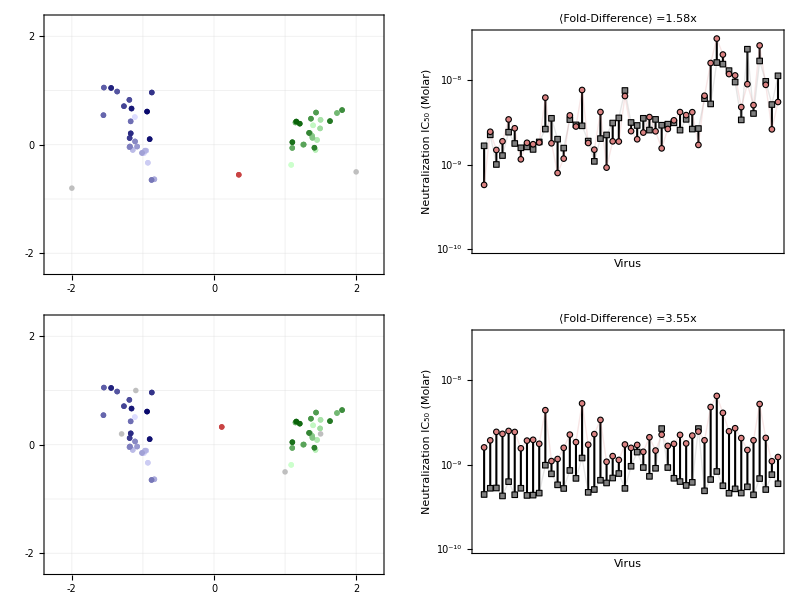

```mathematica
Grid[Block[{markerAbSize=0.15},
Table[
meanFoldDifference=bestmAbDecomposition[antibodies];
{Show[createLandscape[{Association@Thread[orderedVirus->Last@coordsmMDS],
Association@{}},PlotRange->2.3{{-1,1},{-1,1}}],ListPlot[antibodies,PlotStyle->colorAbInMixture,PlotMarkers->markerAb[markerAbSize]],ListPlot[{{x,y}/.bestmAb},PlotStyle->colorAbDecomposition,PlotMarkers->markerAb[markerAbSize]],FrameTicksStyle->20],ListPlot[{mixtureIC50,mAbIC50/.bestmAb},ScalingFunctions->"Log",Joined->True,PlotMarkers->{plotMarker[0.05,"Type"->"Square"],plotMarker[0.05]},PlotStyle->(Directive[#,Opacity[0.2],Thickness[Medium]]&/@{Gray,Lighter@colorAbDecomposition}),Prolog->{Black,Thickness[0.005],MapIndexed[Line[{{First@#2,First@#},{First@#2,Last@#}}]&,Log@Transpose@{mixtureIC50,mAbIC50/.bestmAb}]},ImageSize->300,PlotLabel->Row[{"⟨Fold-Difference⟩ =",Round[meanFoldDifference,0.01],"x"}],Frame->{True,True,False,False},FrameTicks->{MapIndexed[{First@#2,Graphics[{plotStyleVirus@#,markerVirus["Opacity"->1,"OpacityFaceFormFactor"->1][[1,1]]},ImageSize->10]}&,orderedVirus],},FrameLabel->(font[#,12]&/@{"Virus","Neutralization IC_50 (Molar)"}),PlotRange->{ 10^-10,3.45 10^-8},PlotRangeClipping->False,FrameTicksStyle->Directive[12,GrayLevel[0.4]]]}
,{antibodies,{{{-2.,-0.8},{2,-0.5}},{{-1.3,0.2},{1,-0.5},{-1.1,1.},{1.5,0.2}}}}]
],Spacings->{3,2}]
```

#### Degeneracy for n-Antibody Mixtures

Exploring the general case of random n-antibody mixtures, although we restrict the antibodies to lie within rectangles around the H1N1 and H3N2 virus subtypes (since antibodies further away represent the uninteresting case of weak antibodies that do not change the neutralization profile).

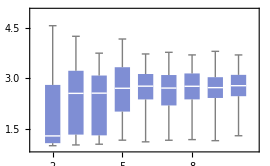

```mathematica
(*resMixtures=Table[
SeedRandom[12345];
Table[{n,bestmAbDecomposition[RandomPoint[RegionUnion[Rectangle[{-2,-0.5},{-0.5,1}],Rectangle[{1,-0.5},{2,0.5}]],n]]},{replicates,100}]
,{n,2,10}];
Iconize[resMixtures,"Mixture Decomposed as mAbs",Method->Compress]*)
resMixtures=;
tickSize=16;
exportPlot=BoxWhiskerChart[resMixtures[[All,All,-1]](*,"Outliers"*),ChartStyle->RGBColor[0.4992, 0.5552, 0.8309304],ImageSize->270,FrameTicksStyle->tickSize,ChartLabels->(font[#,tickSize]&/@Range[2,10]),PlotRange->{{0.2,9.7},{0.9,5}},PlotRangePadding->None]
```

### Figure S1: Comparing Embedding with Matrix Completion

Matrix completion presents an alternative method to fill in missing values, which can offset many of the embedding algorithms analyzed in this work. The code below shows how the distance matrix in Figure 4A can be completed using the robust PCA in the initialization section.

```mathematica
(* To account for bounded measurements, GreaterThan[val]:>val for matrix completion. Afterwards, any value >1.5·10^-7M gets transformed into GreaterThan[1.5·10^-7M] *)
distMatrix=RPCA[neutralizationData[[All,All,3]]/.GreaterThan[val_]:>val,"ShiftType"->Mean,"LogData"->True,"InvertData"->True]/.val_/;val>=1.5 10^-7:>GreaterThan[1.5 10^-7];
(* Convert to Log10 *)
distMatrix=distMatrix/.val_Real:>Log10[val/10^-10];
posGreaterThan=Position[distMatrix,_GreaterThan,Heads->False];
posMissing=Position[distMatrix,_Missing,Heads->False];
dataAbVirusMatrix=MapAt[Item["-",Background->colorMissing]&,MapAt[Item[Row[{font[">"],#[[1]]}],Background->colorGreaterThan]&,distMatrix/.val_Real:>font[Round[val,0.1]],posGreaterThan],posMissing];
Grid[Prepend[Transpose@Prepend[dataAbVirusMatrix,MapIndexed[Graphics[{plotStyleVirus@#,markerVirus["Opacity"->1,"OpacityFaceFormFactor"->1][[1,1]]},ImageSize->20]&,orderedVirus]],Prepend[ConstantArray[Graphics[{colorAbInMixture,markerAb["Thickness"->0.01][[1,1]]},ImageSize->20],First@Dimensions@dataAbVirusMatrix],""]]]
```

| -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | >3.2 | >3.2 | 2.4 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 0.9 | 2.8 | 1.8 | 1. | 2.7 | 2.4 | 0.5 | 1. | -0.1 | 0.3 | 0.3 | 0.5 | 0.4 | 0. | 0.6 | 0.7 | -0.1 | 0.8 | 0.5
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | 3. | 3. | >3.2 | 3. | >3.2 | >3.2 | 2.6 | 2. | 2.8 | 2.6 | 2.3 | 2. | 0.7 | 1.2 | 1.3 | 1.4 | 1.5 | 0.9 | 1.4 | 1.3 | 0.7 | 1.4 | 1.5
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | 3. | 3. | >3.2 | 2.9 | >3.2 | >3.2 | 2.5 | 2. | 2.7 | 2.3 | 1.4 | 1.2 | 1. | 1.2 | 1.3 | 1. | 0.8 | 0.8 | 1.2 | 1.2 | 0.8 | 1.2 | 1.1
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 1.8 | 2.7 | 2.7 | 2. | 1.7 | 1. | 1. | 1.1 | 0.9 | 1.1 | 1.1 | 1.3 | 1.5 | 0.8 | 1.4 | 0.8
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | 3. | 3. | >3.2 | 3. | >3.2 | >3.2 | 2.6 | 2. | 2.8 | 2.6 | 2.7 | 2.4 | 0.6 | 1.4 | 1.7 | 1.5 | 1.5 | 1. | 1.4 | 1.3 | 0.9 | 1.4 | 1.1
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.2 | 2.7 | >3.2 | >3.2 | 1.9 | 2.2 | 0.7 | 1.2 | 1.5 | 1.6 | 1.3 | 0.9 | 1.3 | 1.2 | 0.7 | 1.3 | 1.1
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.9 | 1.9 | 2.4 | 1.4 | >3.2 | 2.3 | 1.6 | 1.8 | 0.5 | 1.1 | 0.8 | 1.2 | 1. | 0.7 | 0.8 | 0.8 | 0.7 | 0.9 | 1.
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.8 | 1.5 | 3.1 | 2.3 | 2. | 2. | 0.7 | 1.2 | 1.1 | 1.3 | 1.3 | 0.8 | 1.1 | 1.1 | 0.6 | 1.2 | 1.2
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.7 | >3.2 | 1.9 | >3.2 | 2.7 | 2. | 1.7 | 0.7 | 1. | 1. | 1.2 | 0.9 | 0.9 | 1.3 | 1.5 | 0.8 | 1.5 | 1.
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2. | 2.5 | 2.4 | 2.2 | 2.1 | 0.3 | 0.9 | 1.1 | 1.4 | 1.4 | 1.1 | 1.2 | 1.5 | 0.8 | 1.4 | 1.1
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.3 | >3.2 | >3.2 | 2.8 | 2.9 | 1. | 1.5 | 2.2 | 2.2 | 1.3 | 1.4 | 1.5 | 1.7 | 1. | 1.6 | 1.5
-Graphics- | >3.2 | >3.2 | 2.7 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.1 | 1.9 | >3.2 | 1.7 | >3.2 | >3.2 | 2.3 | 1.6 | 1.1 | 1.7 | 1.7 | 1.6 | 1.4 | 1.1 | 1.5 | 1.8 | 1.3 | 1.5 | 1.7
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | 2.9 | 2.9 | >3.2 | 2.9 | 1.6 | 1.5 | 2.5 | 1.7 | 2.9 | 2.4 | 1.5 | 1.7 | 0.6 | 1. | 1.1 | 1.1 | 0.9 | 0.9 | 1. | 1.3 | 0.8 | 1.2 | 1.2
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.2 | 1.6 | >3.2 | 1.5 | >3.2 | 2.5 | 1.6 | 1.4 | 0.7 | 1.4 | 1.3 | 1.3 | 0.5 | 1. | 1. | 1.1 | 1. | 0.9 | 1.3
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | 3. | 2.9 | >3.2 | 2.9 | >3.2 | >3.2 | 2.6 | 1.9 | 2.8 | 2.6 | >3.2 | 2.5 | 0.8 | 1.4 | 1.6 | 1.6 | 1.3 | 0.9 | 1.5 | 1.3 | 1.1 | 1.5 | 1.4
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.3 | 1.9 | >3.2 | >3.2 | >3.2 | 2.3 | 0.9 | 1.2 | 1.4 | 1.5 | 1.3 | 1.2 | 1.3 | 1.5 | 1. | 1.5 | 1.6
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.3 | >3.2 | >3.2 | >3.2 | >3.2 | 1.3 | 1.6 | 1.8 | 2. | 1.9 | 1.4 | 1.2 | 1.6 | 1.4 | 1.4 | 1.2
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | 3. | 3. | >3.2 | 2.9 | >3.2 | 2.9 | 2.6 | 1.9 | 2.8 | 2.5 | 2.3 | 2. | 0.7 | 1. | 1.1 | 1.1 | 1.1 | 0.8 | 1.3 | 1.3 | 0.7 | 1.4 | 1.4
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | 3. | 3. | >3.2 | 3. | >3.2 | >3.2 | 2.6 | 1.7 | 2.8 | 2.5 | 2.6 | 2.1 | 0.4 | 0.6 | 1.1 | 0.8 | 0.7 | 0.3 | 0.8 | 1. | 0.5 | 1.2 | 0.6
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2. | >3.2 | >3.2 | >3.2 | 2.8 | 1.1 | 1.3 | 1.2 | 1.7 | 1.6 | 0.9 | 1. | 1. | 0.9 | 1.2 | 1.
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2. | 2.2 | 2.7 | 1.6 | 1.4 | >3.2 | >3.2 | 1.8 | 1.7 | 1.4 | 1. | 1.4 | 0.8 | 1.3 | 1.2 | 0.6 | 1. | 1. | 1.2 | 1. | 1.5
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | 2.9 | 2.8 | 2.2 | 2.6 | >3.2 | 2.6 | 2.2 | 2.2 | 2.7 | 2.2 | 2.1 | 1.6 | 0.9 | 1.8 | 1.7 | 1.4 | 1.4 | 1. | 1.5 | 1.3 | 1.4 | 1.4 | 1.3
-Graphics- | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2 | 2.2 | 2.1 | >3.2 | 2.6 | 1.7 | >3.2 | >3.2 | 2.2 | 2.2 | 1.7 | 1.2 | 1.9 | 1.8 | 1.8 | 1.5 | 1. | 1.4 | 1.4 | 1.4 | 1.3 | 1.4
-Graphics- | 1.6 | 1.4 | 1.1 | 1.7 | 2.2 | 2.8 | 1.8 | 2.2 | 1.3 | 1.3 | 2.1 | 1.8 | >3.2 | 3. | 1.9 | >3.2 | 1.3 | 1.7 | 1.5 | 2.1 | 2. | 2.5 | 2.1 | >3.2 | >3.2 | >3.2 | >3.2
-Graphics- | 1.3 | 0.9 | 1. | 1.4 | 1.6 | 1.9 | 1.7 | 1.6 | 0.7 | 1.2 | 1.5 | 1.3 | 2.2 | 2. | 1.3 | 2.6 | 1.3 | 1.3 | 1.2 | 1.6 | 2.1 | 2.3 | 2.2 | 2.7 | >3.2 | 3. | >3.2
-Graphics- | 1.3 | 0.7 | 0.8 | 1.2 | 1.1 | 1.6 | 1.5 | 1. | 0.7 | 0.9 | 1.1 | 0.9 | 2.2 | 1.6 | 1.2 | 2.3 | 1.3 | 1.3 | 1.2 | 1.4 | 1.6 | 2.4 | 1.1 | >3.2 | >3.2 | >3.2 | >3.2
-Graphics- | 1.4 | 0.6 | 0.6 | 1. | 1.8 | 2.4 | 1.3 | 1.7 | 0.3 | 0.7 | 1.8 | 1.4 | 2.3 | 2.5 | 1.1 | 2.1 | 1.4 | 1.1 | 0.9 | 1.3 | 2.1 | 1.9 | 2. | >3.2 | >3.2 | >3.2 | >3.2
-Graphics- | 1.3 | 0.9 | 0.9 | 1.5 | 1.6 | 1.8 | 1.5 | 1.5 | 0.5 | 1.4 | 1.5 | 1.4 | 2.1 | 2. | 1.7 | 2.8 | 1.4 | 1.3 | 1.5 | 1.9 | 2.2 | 2.4 | 2.3 | 2.7 | >3.2 | 3. | >3.2
-Graphics- | 1.6 | 1.1 | 0.9 | 1.4 | 1.7 | 1.9 | 1.5 | 1.5 | 0.9 | 1. | 1.5 | 1.3 | 2.2 | 2. | 1.7 | 2.5 | 1.2 | 1.4 | 1.4 | 1.5 | 1.6 | 2.6 | 2.2 | 2.7 | >3.2 | 3. | >3.2
-Graphics- | 1.4 | 0.7 | 0.5 | 0.8 | 0.7 | 0.8 | 1. | 0.3 | 0.4 | 0.9 | 0.5 | 0.1 | 2.3 | 0.9 | 1.4 | 2.3 | 1. | 1.6 | 1.2 | 1.3 | 1.6 | 1.3 | 1.4 | 1.9 | >3.2 | >3.2 | >3.2
-Graphics- | 1.5 | 1. | 1. | 1.3 | 1.6 | 1.8 | 1.5 | 1.5 | 0.9 | 1.1 | 1.4 | 1.3 | 2.2 | 1.9 | 1.6 | 2.6 | 1.5 | 1.5 | 1.4 | 1.5 | 1.8 | 2.2 | 2.2 | 2.6 | >3.2 | 2.9 | >3.2
-Graphics- | 1.3 | 1.2 | 0.9 | 1.2 | 1.7 | 1.9 | 1.2 | 1.5 | 0.8 | 1.1 | 1.3 | 1.4 | 2.5 | 2.3 | 1.6 | 2.5 | 1.2 | 1.5 | 1.6 | 1.5 | 1.7 | 1.8 | >3.2 | 2.7 | >3.2 | 3. | >3.2
-Graphics- | 1.5 | 0.9 | 0.9 | 1.3 | 1.6 | 1.8 | 1.5 | 1.5 | 0.8 | 1.3 | 1.5 | 1.4 | 2.2 | 2. | 1.7 | 3. | 1.5 | 1.6 | 1.7 | 1.8 | 2.2 | 2.2 | 2.3 | 2.7 | >3.2 | 3. | >3.2
-Graphics- | 1.6 | 1.1 | 1.1 | 1.4 | 1.7 | 1.8 | 1.7 | 1.5 | 1. | 1.3 | 1.3 | 1.4 | 2.3 | 2.1 | 1.7 | 2.6 | 1.7 | 1.7 | 1.5 | 1.6 | 2. | 2.3 | 2.3 | >3.2 | >3.2 | >3.2 | >3.2
-Graphics- | 1.3 | 1. | 0.9 | 1.5 | 1.6 | 1.8 | 1.7 | 1.6 | 1. | 0.9 | 1.6 | 1.4 | 2.1 | 2. | 1.8 | 2.8 | 1.8 | 1.5 | 1.4 | 1.8 | 2.1 | 2.6 | 2.4 | 2.7 | >3.2 | 3. | >3.2
-Graphics- | 1. | 0.8 | 0.7 | 0.8 | 0.7 | 0.9 | 0.7 | 0.6 | 0.5 | 0.7 | 0.4 | 0.1 | 1.2 | 0.8 | >3.2 | 2.1 | 0.6 | 1. | 1. | 0.8 | 1.3 | 1.5 | 2.1 | 2.6 | >3.2 | >3.2 | >3.2
-Graphics- | 1.7 | 1.5 | 1.1 | 1.7 | 1.8 | 1.9 | 1.5 | 1.6 | 1.4 | 1.8 | 1.6 | 1.5 | 2.2 | 2.1 | >3.2 | >3.2 | 1.6 | 1.5 | 1.8 | 1.7 | 2.3 | 2.3 | 2.5 | 2.7 | >3.2 | 3. | >3.2
-Graphics- | 1.7 | 1.8 | 1.3 | 1.6 | 1.7 | 1.8 | 1.6 | 1.7 | 1.3 | 1.6 | 1.8 | 1.7 | 2.2 | 2.3 | >3.2 | >3.2 | 1.4 | 2. | >3.2 | >3.2 | 1.6 | 2.7 | 2.6 | 2.6 | >3.2 | 2.8 | >3.2
-Graphics- | 2.3 | 2. | 1.7 | 2.7 | 3. | 2.9 | 1.7 | 2.1 | >3.2 | 2.4 | 2.2 | 2.3 | 2.6 | 2.8 | >3.2 | >3.2 | 2.2 | 2.2 | 2.5 | 2.4 | 3. | 3.1 | >3.2 | >3.2 | >3.2 | >3.2 | >3.2
-Graphics- | 2.3 | 2. | 1.6 | 2.4 | 3.1 | 2.8 | 1.7 | 2.1 | >3.2 | 2.2 | 2.2 | 2.2 | 2.4 | 2.7 | >3.2 | >3.2 | 2. | 2. | 2.2 | 2.1 | 2.4 | 3. | >3.2 | >3.2 | >3.2 | >3.2 | >3.2
-Graphics- | 2.1 | 1.7 | 1.4 | 2.7 | 2.3 | 2.3 | 1.8 | 1.9 | >3.2 | 2. | 1.9 | 2. | 2.1 | 2.1 | >3.2 | >3.2 | 1.7 | 1.8 | 1.8 | 1.9 | 2.7 | 2.8 | >3.2 | 2.7 | >3.2 | 3. | >3.2
-Graphics- | 2.2 | 1.7 | 1.5 | 2.1 | 2.1 | 2.2 | 1.9 | 1.9 | 1.7 | 1.8 | 2. | 1.9 | 2.3 | 2.4 | 2.5 | >3.2 | 1.8 | 2. | 2.2 | 2.2 | 2.5 | 2.8 | 2.6 | 2.7 | >3.2 | 2.8 | >3.2
-Graphics- | 1.2 | 1.3 | 0.8 | 1.7 | 1.6 | 1.8 | 1.4 | 1.5 | 1.5 | 1.4 | 1.5 | 1.5 | 2.2 | 1.9 | 2. | 2.8 | 1.4 | 1.7 | 1.8 | 1.9 | 1.8 | 2.5 | 2.5 | 2.6 | >3.2 | 3. | >3.2
-Graphics- | 1.7 | 2.3 | 2.3 | >3.2 | 2.4 | 2.4 | 2.5 | 2.2 | 2.2 | 2. | 2.1 | 1.9 | 2.1 | 2.3 | >3.2 | >3.2 | 2.2 | 1.7 | 1.8 | 1.7 | 2.3 | 2.2 | >3.2 | 2.3 | >3.2 | 2.6 | >3.2
-Graphics- | 1.4 | 1.4 | 1.1 | 1.6 | 1.5 | 1.8 | 1.7 | 1.5 | 1.6 | 1.4 | 1. | 1.2 | 2.5 | 2.1 | 2.1 | 2.8 | 1.5 | 1.8 | 1.9 | 1.9 | 1.9 | 2.3 | >3.2 | 2.3 | >3.2 | >3.2 | >3.2
-Graphics- | 1.5 | 2. | 1.8 | 2.4 | 3. | 3. | 2. | 2.6 | 3. | 2.4 | 2.3 | 2.8 | 3.1 | 2.8 | 2.5 | >3.2 | 2.1 | 1.9 | 2.2 | 2.1 | 2.9 | 3. | >3.2 | >3.2 | >3.2 | >3.2 | >3.2
-Graphics- | 1.6 | 2. | 1.8 | 2.3 | 1.6 | 2.2 | 2. | 1.7 | 2.8 | 2.2 | 1.4 | 1.7 | 2.3 | 1.9 | 2.6 | >3.2 | 1.9 | 2. | 2.1 | 2.2 | 2.6 | 2.4 | 2.9 | 2.1 | >3.2 | >3.2 | >3.2
-Graphics- | 1.2 | 1.5 | 1.2 | 1.7 | 1.5 | 1.7 | 1.6 | 1.2 | 2.1 | 1.5 | 1. | 1.3 | 2. | 1.4 | 1.9 | 2.5 | 1.4 | 1.5 | 1.6 | 1.6 | 1.8 | 2.2 | 2.1 | 1.7 | >3.2 | >3.2 | >3.2
-Graphics- | 1.5 | 1.8 | 1.7 | 2. | 2. | 2.2 | 2. | 1.8 | 2.1 | 1.8 | 1.7 | 1.7 | 2.4 | 2.2 | 2.2 | >3.2 | 1.4 | 1.7 | 1.7 | 1.9 | 2.3 | 2. | 2.4 | 2.4 | >3.2 | 2.9 | >3.2

### Figure S2: Bipartite MDS, comparing SDP relaxation vs Numeric Minimization

We compare two methods of performing bipartite MDS on synthetic data, namely, determining the affine transformations A_U and A_V via SDP or using numeric minimization. Results are canned for speed, with the relevant code in the initialization section.

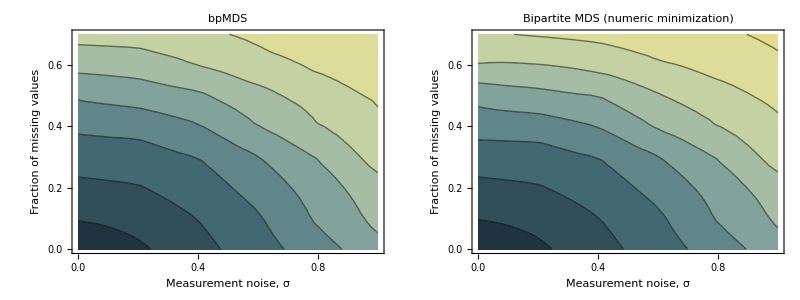

```mathematica
Grid[{{drawPhaseDiagram[dataPhaseDiagram,"cMDS",MaxPlotPoints->25,InterpolationOrder->1,"Examples"->{}],Show[drawPhaseDiagram[dataPhaseDiagramExtra,"cMDSnumeric",MaxPlotPoints->25,InterpolationOrder->1,"Examples"->{}],PlotLabel->"Bipartite MDS (numeric minimization)"]
}},Spacings->2]
```

### Figure S3: Rigidity of Positions

Not all antibodies or viruses may conform to the tight restrictions of a 2D geometry, either because of large experimental error or because some entries exhibit fundamentally different behavior. We test for this scenario by recomputing the embedding with one of the 51 viruses or 27 antibodies removed, checking whether any entries substantially shifted across these embeddings. In other words, if an entry’s position substantially changes due to a small perturbation (like removing another entry), then its position is not robust and we remove it in our subsequent analysis.

#### Panel A: Identifying Outliers

We rerun the embedding using metric MDS with one entry removed. The final embeddings are aligned as closely as possible to a previous embedding from Einav 2023https://doi.org/10.1038/s43588-022-00375-1Nonehttps://doi.org/10.1038/s43588-022-00375-1HyperlinkActionRecycledHyperlinkActive, and the scatter of each antibody or virus is computed.

```mathematica
(* Neutralization Landscape coordinates from Einav 2023https://doi.org/10.1038/s43588-022-00375-1Nonehttps://doi.org/10.1038/s43588-022-00375-1HyperlinkActionRecycledHyperlinkActive, used for initialization *)
{coordsVirusStem,coordsAbStem}=Map[{0.05,-0.4}+#&,{,},{2}];
(* Distance matrix *)
distMatrix=neutralizationData[[All,All,-1]]/.val_Real:>Log10[val/10^-10.];
```

```mathematica
(*(* Remove one of the viruses, re-compute MDS *)
Do[
coordsVirusRemoved[orderedVirus[[indexVirusToRemove]]]=metricMDS[Transpose@Delete[Transpose@distMatrix,indexVirusToRemove],"SearchMethod"->Automatic,"SearchPoints"->1,"Comparing"->"Distance","PenalizeError"->"MeanSquaredError","InitialPoints"->{coordsVirusStem/@Delete[orderedVirus,indexVirusToRemove],coordsAbStem/@orderedAbStem}];
(* Align solutions and extract entry position *)
trans=transform[Join[coordsAbStem/@orderedAbStem,coordsVirusStem/@Delete[orderedVirus,indexVirusToRemove]],Join@@coordsVirusRemoved[orderedVirus[[indexVirusToRemove]]]];
(* Match mMDS as closely as possible *)
transformed[orderedVirus[[indexVirusToRemove]]]=Map[trans,coordsVirusRemoved[orderedVirus[[indexVirusToRemove]]],{2}];
,{indexVirusToRemove,1,Last@Dimensions@distMatrix}];
(* Remove one of the antibody, re-compute MDS *)
Do[
coordsAbRemoved[orderedAbStem[[indexAbToRemove]]]=metricMDS[Delete[distMatrix,indexAbToRemove],"SearchMethod"->Automatic,"SearchPoints"->1,"Comparing"->"Distance","PenalizeError"->"MeanSquaredError","InitialPoints"->{coordsVirusStem/@orderedVirus,coordsAbStem/@Delete[orderedAbStem,indexAbToRemove]}];
(* Align solutions and extract entry position *)
trans=transform[Join[coordsAbStem/@Delete[orderedAbStem,indexAbToRemove],coordsVirusStem/@orderedVirus],Join@@coordsAbRemoved[orderedAbStem[[indexAbToRemove]]]];
(* Match mMDS as closely as possible *)
transformed[orderedAbStem[[indexAbToRemove]]]=Map[trans,coordsAbRemoved[orderedAbStem[[indexAbToRemove]]],{2}];
,{indexAbToRemove,1,First@Dimensions@distMatrix}];
assoc=Association@Table[
removedEntry->Association@Join[Thread[DeleteCases[orderedAbStem,removedEntry]->First@transformed[removedEntry]],Thread[DeleteCases[orderedVirus,removedEntry]->Last@transformed[removedEntry]]]
,{removedEntry,Join[orderedAbStem,orderedVirus]}];*)
assoc=;
```

```mathematica
(* Standard deviation in {x,y} for every antibody/virus *)
resAb=Association@Table[
pnts=assoc[#][entry]&/@DeleteCases[Keys@assoc,entry];
entry->StandardDeviation/@Transpose[pnts]
,{entry,orderedAbStem}];
resVirus=Association@Table[
pnts=assoc[#][entry]&/@DeleteCases[Keys@assoc,entry];
entry->StandardDeviation/@Transpose[pnts]
,{entry,orderedVirus}];
worstAbs=Echo[Keys@ReverseSortBy[resAb,Norm][[;;5]],"5 worst Abs:"];
worstViruses=Echo[Keys@ReverseSortBy[resVirus,Norm][[;;5]],"5 worst Viruses:"];
```

5 worst Abs:  {22-1B08,55-1D06,02-1B02,58-6F03,CR6261}

5 worst Viruses:  {H3N2 A/Switzerland/9715293/2013,H3N2 A/Singapore/INFIMH-160019/2016,H3N2 A/Moscow/10/1999,H3N2 A/Hong Kong/4801/2014,H3N2 A/Indiana/10/2011}

The five worst antibodies and five worst viruses are removed in our subsequent analyses. The following plot shows the scattered positions of these worst antibodies and viruses on the backdrop of the remaining entries.

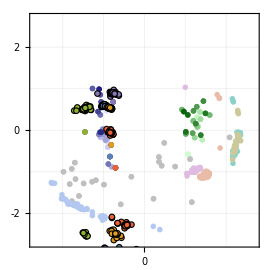

```mathematica
assocVir=Association@Table[
entry->Mean[assoc[#][entry]&/@DeleteCases[Keys@assoc,entry]]
,{entry,orderedVirus}];
assocAb=Association@Table[
entry->Mean[assoc[#][entry]&/@DeleteCases[Keys@assoc,entry]]
,{entry,orderedAbStem}];
Show[createLandscape[{assocVir,assocAb},"MarkerVirusOpacity"->0.03,"MarkerAbOpacity"->0.07],
ListPlot[List/@assocVir/@worstViruses,PlotMarkers->markerVirus[0.13,"Opacity"->1,"Thickness2"->0.02]],
ListPlot[List/@assocAb/@worstAbs,PlotStyle->Lighter/@ColorData[95]/@Range@5,PlotMarkers->markerAb[0.13,"Thickness"->0.025]],ListPlot[Table[assoc[#][entry]&/@DeleteCases[Keys@assoc,entry],{entry,worstViruses}],PlotMarkers->plotMarker[0.035]],ListPlot[Table[assoc[#][entry]&/@DeleteCases[Keys@assoc,entry],{entry,worstAbs}],PlotMarkers->plotMarker[0.04,"Type"->"Diamond"],PlotStyle->Lighter/@ColorData[95]/@Range@5]]
```

#### Panel B: Leave-Some-Out Analysis - Full Dataset

We withhold 10% of the antibody-virus interactions, rerun an embedding, and predict the withheld values. This process is repeated 10 times. The following plot shows the results using the full dataset (without withholding the 5 worst antibodies and 5 worst viruses from Panel A).

```mathematica
runRemoval[{},{"mMDS","cMDS","SDP"},10]
```

-Graphics-

#### Panel C: Leave-Some-Out Analysis - Removing top 5 virus/antibody outliers

As an Panel B, we withhold and predict 10% of the antibody-virus interactions, this time after withholding the 5 worst antibodies and 5 worst viruses from Panel A. Note that RMSE=0.52 of SDP improves while the RMSE=0.49 of metric MDS gets worse, but importantly, their errors are now comparable (as would be expected of two embedding methods that leverage the underlying structure of the data).

```mathematica
runRemoval[Join[Keys@ReverseSortBy[resVirus,Norm][[;;5]],Keys@ReverseSortBy[resAb,Norm][[;;5]]],{"mMDS","cMDS","SDP"},10]
```

-Graphics-

### Figure S4: Rank of SDP - Phase Diagram Plot

Another way to approximate the rigidity of the system is by computing the rank of the positive-semidefinite matrix G, with higher rank representing a less rigid framework.

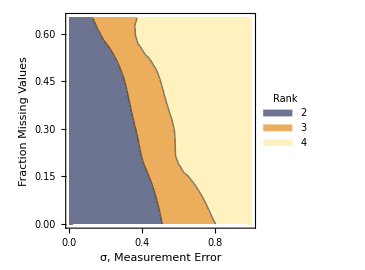

```mathematica
ListContourPlot[,InterpolationOrder->1,MaxPlotPoints->25,Contours->{1,3,4},PlotRangePadding->None,FrameTicksStyle->16,FrameLabel->(font[#,18]&/@{"σ, Measurement Error","Fraction Missing Values"}),ImageSize->270,PlotRange->{{0,1},{0,0.65}},PlotLegends->Placed[SwatchLegend[{RGBColor[0.4274509388002017, 0.45490190530236546, 0.5686274150337474],RGBColor[0.9254902344335256, 0.6784314370253509, 0.36470585663126764],RGBColor[1., 0.9490195325179408, 0.7490196957166956]},font[#,12]&/@{2,3,4},LegendLabel->Placed[font["Rank",14,Bold],Above],LegendFunction->frame],Scaled[{{0.85,0.77},{0.5,0.5}}]]]
```

### Figure S5: Annotated Antibody-Virus Data

The annotated antibody-virus dataset from Einav 2023https://doi.org/10.1038/s43588-022-00375-1Nonehttps://doi.org/10.1038/s43588-022-00375-1HyperlinkActionRecycledHyperlinkActive.

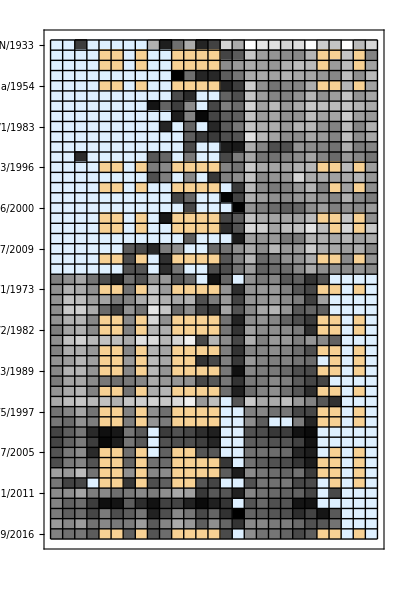
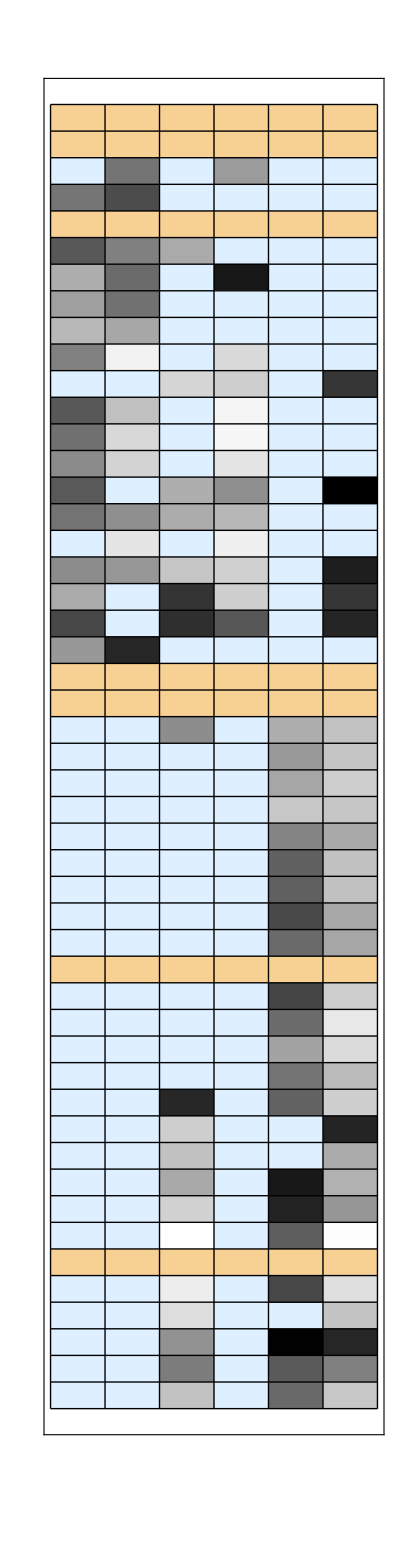

```mathematica
{(* Neutralization of HA stem-targeting antibodies *)
plotData=neutralizationData[[All,All,3]]/.val_Real:>Log10[val/10^-10];
arrayPlotAbVirusFull=ArrayPlot[Transpose@plotData,PlotRangePadding->None,ImageSize->{Automatic,600},ColorFunctionScaling->False,Frame->True,Mesh->True,MeshStyle->Directive[Black,Thin],ColorRules->{_Missing->colorMissing,_GreaterThan->colorGreaterThan,val_Real:>GrayLevel[1-Rescale[val,MinMax@DeleteCases[Flatten@plotData,_Missing|_GreaterThan]]]},FrameTicks->{MapIndexed[{First@#2,Row[{font[StringReplace[#,{"-"->"-"}],9]," ",Graphics[{plotStyleVirus@#,markerVirus["Opacity"->1,"OpacityFaceFormFactor"->1][[1,1]]},ImageSize->16]}]}&,orderedVirus],None,None,MapIndexed[{First@#2,Column[{Rotate[font[StringReplace[#,{"-"->"-"}],10],π/2],Graphics[{colorAbInMixture,markerAb["Thickness"->0.01][[1,1]]},ImageSize->15]},Alignment->Center]}&,orderedAbStem]},AspectRatio->1.5],
(* Neutralization of HA head-targeting antibodies *)
neutralizationDataHeadAbs=;
orderedAbHead=neutralizationDataHeadAbs[[All,1,2]];
plotData=neutralizationDataHeadAbs[[All,All,3]]/.val_Real:>Log10[val/10^-10];
arrayPlotAbVirusFull=ArrayPlot[Transpose@plotData,PlotRangePadding->None,ImageSize->{Automatic,600},AspectRatio->8,ColorFunctionScaling->False,Frame->True,Mesh->True,MeshStyle->Directive[Black,Thin],ColorRules->{_Missing->colorMissing,_GreaterThan->colorGreaterThan,val_Real:>GrayLevel[1-Rescale[val,MinMax@DeleteCases[Flatten@plotData,_Missing|_GreaterThan]]]},FrameTicks->{None,None,None,MapIndexed[{First@#2,Column[{Rotate[font[StringReplace[#,{"-"->"-"}],10],π/2],Graphics[{Lighter[RGBColor[0.45512466979723104, 0.30561986937551394, 0.19969653154271888],0.2],markerAb["Thickness"->0.01][[1,1]]},ImageSize->15]},Alignment->Center]}&,orderedAbHead]},AspectRatio->1.5]
}
```

### Figure S6: Comparing different mMDS loss functions

We assess different choices of loss function for metric MDS and show how capably they handle large outliers or systematic error.

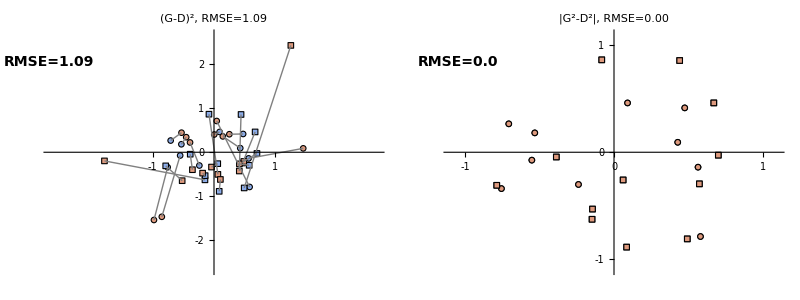

```mathematica
(* Handling large outliers *)
{nVirus,nAb}={10,12};
outliers={{1,1},{2,2},{3,1}}->10;
{coords,distMatrix}=exampleData[{nVirus,nAb},0.];
distMatrixOutliers=ReplacePart[distMatrix,outliers];
(* cMDS and SDP on outlier data *)
coordsmMDSPower1=metricMDS[distMatrixOutliers,"SearchMethod"->Automatic,"SearchPoints"->Automatic,"Comparing"->"DistanceSquared","PenalizeError"->"MeanAbsoluteError"];
resMetricMDSPower1=Show[analyzeMDS[coords,coordsmMDSPower1,"ShowLegend"->False,"AddToPlotLabel"->Row[{" |G^2-D^2|, "}],"PlotLabelSize"->15,"ConnectNumericToActual"->True,"Comparing"->"Distance","PenalizeError"->"RMSE","ErrorLabel"->"RMSE",PlotRange->1.1{-1,1},PlotStyle->colorsEmbedding],Ticks->ConstantArray[,2],Epilog->{Text[font[Row[{"RMSE=",format[errorActualCoords[coordsmMDSPower1,coords,"Comparing"->"Distance","PenalizeError"->"RMSE"],1]}],14,Bold,Background->Directive[White,Opacity[0.5]]],{-1.05,0.84},{-1,0}]}];
coordsmMDSPower2=metricMDS[distMatrixOutliers,"SearchMethod"->Automatic,"SearchPoints"->Automatic,"Comparing"->"Distance","PenalizeError"->"MeanSquaredError"];
resMetricMDSPower2=Show[analyzeMDS[coords,coordsmMDSPower2,"ShowLegend"->False,"AddToPlotLabel"->Row[{" (G-D)^2, "}],"PlotLabelSize"->15,"ConnectNumericToActual"->True,"Comparing"->"Distance","PenalizeError"->"RMSE","ErrorLabel"->"RMSE","OverrideLabel"->{"X^*","X","Y^*","Y"},PlotStyle->colorsEmbedding],Ticks->ConstantArray[,2],Epilog->{Text[font[Row[{"RMSE=",Round[errorActualCoords[coordsmMDSPower2,coords,"Comparing"->"Distance","PenalizeError"->"RMSE"],0.01]}],14,Bold,Background->Directive[White,Opacity[0.5]]],{-2.7,2.06},{-1,0}]}];
Grid[{{resMetricMDSPower2,resMetricMDSPower1}}]
```

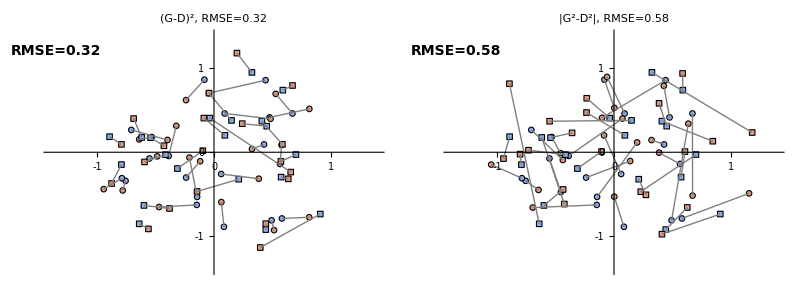

```mathematica
(* Handling large outliers *)
{nVirus,nAb}={20,20};
{coords,distMatrix}=exampleData[{nVirus,nAb},1.];
(* cMDS and SDP on outlier data *)
coordsmMDSPower1=metricMDS[distMatrix,"SearchMethod"->Automatic,"SearchPoints"->Automatic,"Comparing"->"DistanceSquared","PenalizeError"->"MeanAbsoluteError"];
resSystematicErrorPower1=Show[analyzeMDS[coords,coordsmMDSPower1,"ShowLegend"->False,"AddToPlotLabel"->Row[{" |G^2-D^2|, "}],"PlotLabelSize"->15,"ConnectNumericToActual"->True,"Comparing"->"Distance","PenalizeError"->"RMSE","ErrorLabel"->"RMSE",PlotRange->1.4{-1,1},PlotStyle->colorsEmbedding],Ticks->ConstantArray[,2],Epilog->{Text[font[Row[{"RMSE=",Round[errorActualCoords[coordsmMDSPower1,coords,"Comparing"->"Distance","PenalizeError"->"RMSE"],0.01]}],14,Bold,Background->Directive[White,Opacity[0.5]]],{-1.35,1.2},{-1,0}]}];
coordsmMDSPower2=metricMDS[distMatrix,"SearchMethod"->Automatic,"SearchPoints"->Automatic,"Comparing"->"Distance","PenalizeError"->"MeanSquaredError"];
resSystematicErrorPower2=Show[analyzeMDS[coords,coordsmMDSPower2,"ShowLegend"->False,"AddToPlotLabel"->Row[{" (G-D)^2, "}],"PlotLabelSize"->15,"ConnectNumericToActual"->True,"Comparing"->"Distance","PenalizeError"->"RMSE","ErrorLabel"->"RMSE",PlotRange->1.4{-1,1},"OverrideLabel"->{"X^*","X","Y^*","Y"},PlotStyle->colorsEmbedding],Ticks->ConstantArray[,2],Epilog->{Text[font[Row[{"RMSE=",Round[errorActualCoords[coordsmMDSPower2,coords,"Comparing"->"Distance","PenalizeError"->"RMSE"],0.01]}],14,Bold,Background->Directive[White,Opacity[0.5]]],{-1.35,1.2},{-1,0}]}];
Grid[{{resSystematicErrorPower2,resSystematicErrorPower1}}]
```

We then compare different embedding algorithms in different dimensions. Note the metric MDS 2D result exhibits an “elbow,” which is taken to be an indication that the data is best described by this method and dimensionality.

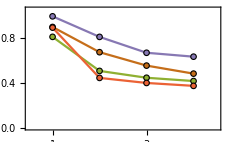

```mathematica
distMatrix=distMatrixAbVirus;
posMeasured=Position[distMatrix,Except[_Missing],{2},Heads->False];
methods={"cMDS","SDP","mMDSunsquared","mMDS"};
crossValidateLeaveSomeOut=;
errorDimensions=Table[Table[
plotData=crossValidateLeaveSomeOut[{method,dim}];
RootMeanSquare[compare@@@plotData]
,{dim,1,4}],
{method,methods}];
Block[{colors=ColorData[97]/@{5,6,3,4}},
ListPlot[errorDimensions,Joined->True,PlotMarkers->plotMarker[0.065],PlotRange->{{0.5,4.5},{0,1.05}},Frame->{True,True,False,False},FrameTicksStyle->14,PlotStyle->colors,FrameTicks->,ImageSize->230]
]
```

### Figure S7: Combining cMDS/SDP with mMDS Post-Processing

Embedding algorithms can be easily combined, with any one serving to initialize metric MDS. These combined algorithms tend to outperform any individual algorithm.

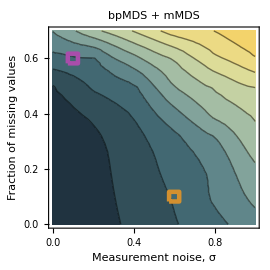
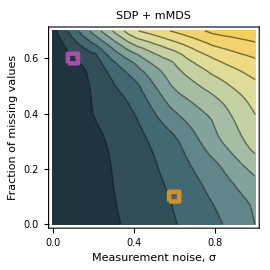
-Graphics- |  | -Graphics- |  | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
methods={"mMDS","cMDS+mMDS","SDP+mMDS"};
legPhaseDigrams=BarLegend[{ColorData["StarryNightColors"],{0,1}},LegendMarkerSize->200,Ticks->({#,If[MemberQ[Range[0,1,0.2],#],format[#,1],""]}&/@Range[0,1,0.1]),LabelStyle->14];
legExamplePlots=PointLegend[ColorData[95]/@{1,2,1,2},font/@{"Virus (Ground Truth)","Virus (Numerical)","Antibody (Ground Truth)","Antibody (Numerical)"},LegendMarkers->{plotMarker[0.05],plotMarker[0.7 0.05],plotMarker[1.125 0.05,"Type"->"Square"],plotMarker[0.7 1.125 0.05,"Type"->"Square"]},LegendFunction->frame];
Grid[{Append[Riffle[Table[drawPhaseDiagram[dataPhaseDiagram,method,MaxPlotPoints->25,InterpolationOrder->1],{method,methods}],SpanFromLeft,{2,-1,2}],legPhaseDigrams],Append[Flatten[drawExamplePlots/@methods],legExamplePlots]},Spacings->{2,2},Alignment->{Left}]
```

### Figure S8: Limits of σ=0 and f_Missing=0

Exploring the behavior of the phase diagram in Figure 2 on the axes, representing either the noise-free limit (σ=0) or the case of complete data with no missing values (f_Missing=0).

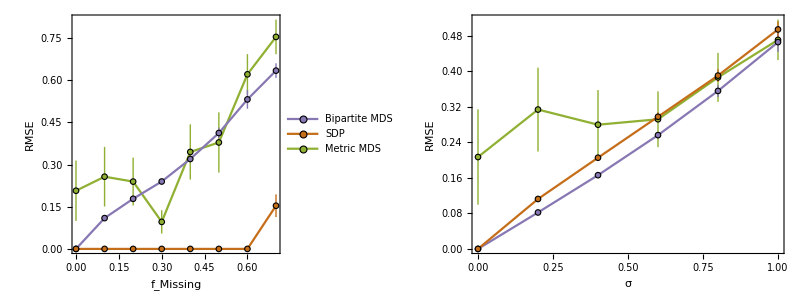

```mathematica
methods={"mMDS","cMDS","SDP"};
plotFracMissing=ListPlot[Table[Cases[dataPhaseDiagram[method],{0.,fMissing_,replicates__}:>{fMissing,MeanAround[First/@{replicates}]}],{method,methods}],AxesOrigin->{0,0},PlotRange->All,PlotStyle->colorsLeaveOneOut,Joined->True,PlotMarkers->plotMarker[0.05],Frame->{True,True,False,False},FrameLabel->(font[#,14]&/@{"f_Missing","RMSE"}),FrameTicksStyle->12,ImageSize->270,PlotLegends->Placed[PointLegend[colorsLeaveOneOut[[{2,3,1}]],font/@{"Bipartite MDS","SDP","Metric MDS"},LegendFunction->frame,LegendMarkers->plotMarker[0.03],Spacings->{0.3,0.2}],Scaled[{{0.28,0.77},{0.5,0.5}}]]];
plotσ=ListPlot[Table[Cases[dataPhaseDiagram[method],{σ_,0.,replicates__}:>{σ,MeanAround[First/@{replicates}]}],{method,methods}],AxesOrigin->{0,0},PlotRange->All,Joined->True,PlotStyle->colorsLeaveOneOut,PlotMarkers->plotMarker[0.05],Frame->{True,True,False,False},FrameLabel->(font[#,14]&/@{"σ","RMSE"}),FrameTicksStyle->12,ImageSize->270];
grid=Grid[{{plotFracMissing,plotσ}},Spacings->{2,2}]
```

### Figure S9: Best 1-Ab and 2-Ab Mixtures

This plot was adapted from Figure 3 of Einav 2023https://doi.org/10.1038/s43588-022-00375-1Nonehttps://doi.org/10.1038/s43588-022-00375-1HyperlinkActionRecycledHyperlinkActive.

### Figure S10: Comparison to Smith 2004 Methods

Here, we follow the traditional antigenic cartography approach from Smith 2004, embedding multiple antibodies binding to different epitopes within the same space. The resulting embedding looks very different, and by using leave-some-out cross-validation, we see that the RMSE=0.55 of this combined embedding is worse than the purely HA stem embedding with an RMSE=0.49 (Figure 4B and 4D).

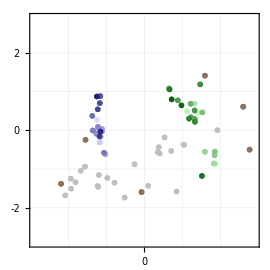

```mathematica
neutralizationDataHeadAbs=;
orderedAbHead=neutralizationDataHeadAbs[[All,1,2]];
(* Neutralization Landscape coordinates from Einav 2023https://doi.org/10.1038/s43588-022-00375-1Nonehttps://doi.org/10.1038/s43588-022-00375-1HyperlinkActionRecycledHyperlinkActive, used for initialization *)
{neutLandscapeCoordsVirus,neutLandscapeCoordsAb}=Map[{0.05,-0.4}+#&,{,},{2}];
(* Outlier antibodies/viruses to remove *)
worstAbs={"22-1B08","55-1D06","02-1B02","58-6F03","CR6261"};
worstViruses={"H3N2 A/Switzerland/9715293/2013","H3N2 A/Singapore/INFIMH-160019/2016","H3N2 A/Moscow/10/1999","H3N2 A/Hong Kong/4801/2014","H3N2 A/Indiana/10/2011"};
removing=Join[worstAbs,worstViruses];
(* Distance matrix *)
distMatrix=Join[neutralizationData,neutralizationDataHeadAbs][[All,All,-1]]/.val_Real:>Log10[val/10^-10.];
distMatrix=Transpose@Delete[Transpose@Delete[distMatrix,Position[orderedAbStem,Alternatives@@removing]],Position[orderedVirus,Alternatives@@removing]];
(* mMDS solution *)
coordsMMDS=metricMDS[distMatrix,"SearchMethod"->Automatic,"SearchPoints"->25,"Comparing"->"Distance","PenalizeError"->"MeanSquaredError","InitialPoints"->{neutLandscapeCoordsVirus/@DeleteCases[orderedVirus,Alternatives@@removing],Join[neutLandscapeCoordsAb/@DeleteCases[orderedAbStem,Alternatives@@removing],ConstantArray[{0,0},Length@orderedAbHead]]}];
(* Align solutions and extract entry position *)
trans=transform[Join[neutLandscapeCoordsAb/@DeleteCases[orderedAbStem,Alternatives@@removing],neutLandscapeCoordsVirus/@DeleteCases[orderedVirus,Alternatives@@removing]],Join@@MapAt[#[[;;Length@orderedAbStem-Length@worstAbs]]&,coordsMMDS,{1}]];
(* Match mMDS as closely as possible *)
resMMDS={Association@Thread[DeleteCases[orderedVirus,Alternatives@@removing]->Last@Map[trans,coordsMMDS,{2}]],Association@Thread[Join[DeleteCases[orderedAbStem,Alternatives@@removing],orderedAbHead]->First@Map[trans,coordsMMDS,{2}]]};
(* Embedding containing the HA head+stem antibodies *)
Show[createLandscape[resMMDS,"Tooltip"->True],createLandscape[{Association@{},resMMDS[[2,-6;;]]},"Tooltip"->True]/.colorAbInMixture->RGBColor[0.5640997358377848, 0.44449589550041113, 0.35975722523417514],PlotRange->2.9{{-1,1},{-1,1}}]
```

Leave-some-out cross-validation, withholding 10% of the interactions and predicting them via the embedding.

```mathematica
(*resLeaveSomeOut=runLeaveSomeOut[distMatrix,{"mMDS"},{2},10];*)
resLeaveSomeOut=;
Echo[RootMeanSquare[compare@@@resLeaveSomeOut[{"mMDS",2}]],"RMSE=",Round[#,0.01]&];
```

RMSE=  0.55

# Initialization

### Embedding Algorithms

#### Background

This notebook contains methods to embed a distance matrix into Euclidean space ℝ^d. We are specifically interested in two problems:

Monopartite embedding [the classic “city-city” problem]: Given a real symmetric distance matrix D_(j,k)∈ℝ^(n×n) between n points and the dimension d, find the best possible configuration of {x_j}_(j=1)^n points in ℝ^d that matches this distance matrix with D_(j,k)≈‖x_j-x_k‖

Bipartite embedding [the “antibody-virus” problem]: Given a real distance matrix D_(j,k)∈ℝ^(m×n) between m points of one category [antibodies] and n points of another [viruses], together with the dimension d, find the best possible configuration of {x_j}_(j=1)^m and {y_k}_(k=1)^n points in ℝ^d that matches the distance matrix with D_(j,k)≈‖x_j-y_k‖

#### Error Function

Options "Comparing"→"Distance" and "PenalizeError"→"RMSE" computes the RMSE

Options "Comparing"→"DistanceSquared" and "PenalizeError"→"MeanAbsoluteError" are the most similar to the error that SDP is minimizing

```mathematica
ClearAll[errorMDS]
Options[errorMDS]={"Comparing"->"DistanceSquared","PenalizeError"->"MeanAbsoluteError","Verbose"->False,"IgnoreEntries"->{},"ReturnMeanError"->True};
errorMDS[coords_,distMatrixRaw_,OptionsPattern[]]:=Block[{distMatrix=distMatrixRaw,belowDynamicRange,aboveDynamicRange,dist,coords1,coords2,slice},
If[SymmetricMatrixQ[distMatrix],
(* City-city distances *)
coords1=coords2=coords;
slice=UpperTriangularize,
(* Antibody-virus distances *)
{coords1,coords2}=coords;
slice=Identity
];

(* Positions of upper/lower bounds *)
belowDynamicRange=Position[distMatrix,_LessThan];
aboveDynamicRange=Position[distMatrix,_GreaterThan];
distMatrix=MapAt[First,distMatrix,Join[belowDynamicRange,aboveDynamicRange]];

(* Compute error. Bounded values only take effect when the bound is not met. For city-city distances, the matrix is symmetric, and only the upper-half slice needs to be considered *)
Switch[OptionValue["Comparing"],
"Distance",
dist=slice[Outer[Sqrt[(#1-#2).(#1-#2)]&,coords1,coords2,1]-distMatrix];
dist=MapAt[#/Sqrt[1.+E^(10. #)]&,dist,aboveDynamicRange];
dist=MapAt[#/Sqrt[1.+E^(-10. #)]&,dist,belowDynamicRange],
"DistanceSquared",
dist=slice[Outer[(#1-#2).(#1-#2)&,coords1,coords2,1]-distMatrix^2];
dist=MapAt[#/Sqrt[1.+E^(10. #)]&,dist,aboveDynamicRange];
dist=MapAt[#/Sqrt[1.+E^(-10. #)]&,dist,belowDynamicRange]
];
dist=Delete[dist,OptionValue["IgnoreEntries"]];
If[!OptionValue["ReturnMeanError"],
Return[Join@@DeleteMissing[dist,2,All]]
];
Switch[OptionValue["PenalizeError"],
"RMSE",RootMeanSquare@Flatten@DeleteMissing[dist,2,All],
"MeanAbsoluteError",Mean@Flatten@Abs@DeleteMissing[dist,2,All],
"RootMeanAbsoluteError",Sqrt@Mean@Flatten@Abs@DeleteMissing[dist,2,All],
"MeanSquaredError",Mean@Flatten[DeleteMissing[dist,2,All]^2]
]
]
```

```mathematica
ClearAll[errorActualCoords]
Options[errorActualCoords]=Join[{"Verbose"->False},
(* Add default option values from errorMDS *)
FilterRules[Options[errorMDS],{"Comparing","PenalizeError"}]];
errorActualCoords[coordsNumeric_,coordsActual_,OptionsPattern[]]:=Block[{level,join,coordsNumericTransformed,error},
If[MatchQ[Dimensions/@coordsActual,{{2}..}],
level=1;
join=List,
level=2;
join=Join
];
(* Apply a rigid transform to align the MDS results as closely as possible to the true solution *)
coordsNumericTransformed=Map[transform[join@@coordsActual,join@@coordsNumeric],coordsNumeric,{level}];
(* Euclidean distance between actual and numeric coordinates *)
error=MapThread[EuclideanDistance,{join@@coordsActual,join@@coordsNumericTransformed}];
If[OptionValue["Comparing"]==="DistanceSquared",
error=error^2
];
Switch[OptionValue["PenalizeError"],
"RMSE",RootMeanSquare@error,
"MeanAbsoluteError",Mean@error,
"RootMeanAbsoluteError",Sqrt@Mean@error,
"MeanSquaredError",Mean[error^2]
]
]
```

#### Helper Functions

```mathematica
(* Centering matrix *)
J[n_Integer]:=IdentityMatrix[n]-ConstantArray[1/n,{n,n}]
```

```mathematica
(* Generate 'numEntries' points in 2D whose distance matrix has error σ *)
(* Return {true coordinates, noisy distance matrix} *)
ClearAll[exampleData]
Options[exampleData]={"SeedRandom"->12345,"Range"->2.,"FractionMissing"->0,"FractionLessThan"->0,"FractionGreaterThan"->0,"MinEntriesRowCol"->2};
exampleData[numEntries:(_Integer|{_Integer,_Integer}),σ_:0.,OptionsPattern[]]:=Block[{fracMissing=OptionValue["FractionMissing"],fracLessThan=OptionValue["FractionLessThan"],fracGreaterThan=OptionValue["FractionGreaterThan"],minEntries=OptionValue["MinEntriesRowCol"],cityCityQ=MatchQ[numEntries,_Integer],coords,coordsVirus,coordsAb,distMatrix,n,m,posMeasured,posWithheld,entry,indices,thresholdSmall,thresholdLarge},
SeedRandom[OptionValue["SeedRandom"]];
If[cityCityQ,
(* City-city distance *)
n=numEntries;
coords=RandomReal[1/2 OptionValue["Range"]{-1,1},{n,2}];
distMatrix=Outer[Sqrt[(#1-#2).(#1-#2)]&,coords,coords,1];
(* Add noise, but keep distance matrix symmetric *)
distMatrix=distMatrix+RandomReal[σ{-1,1},{n,n}];
distMatrix=1/2(distMatrix+Transpose@distMatrix),

(* Antibody-virus distance *)
{m,n}=numEntries;
coords={coordsVirus,coordsAb}=RandomReal[1/2 OptionValue["Range"]{-1,1},{#,2}]&/@{m,n};
distMatrix=Outer[Sqrt[(#1-#2).(#1-#2)]&,coordsVirus,coordsAb,1];
(* Add noise *)
distMatrix=distMatrix+RandomReal[σ{-1,1},{m,n}]
];
(* Withhold values, labeling them as Missing *)
If[fracMissing==0.,
posWithheld={},
If[minEntries===0,
(* Randomly select entries to withhold - for large 'fracMissing' this may lead to rows/columns with ≤1 measurements *)
posMeasured=Position[distMatrix,Except[0.],{2},Heads->False];
posWithheld=RandomSample[posMeasured,Round[fracMissing Length@posMeasured]],

If[cityCityQ,
(* City-city embedding: Ensure there are at least 'minEntries' measured entires in each row, ignoring the zero diagonals *)
Echo["Not implemented","Error!"];Return[$Failed],
(* Antibody-virus embedding: Ensure there are at least 'minEntries' measured entries in each row and column *)
If[minEntries Max[m ,n]>m n(1.-fracMissing),
Echo["MinEntriesRowCol is impossible given the large FractionMissing","Error!"];Return[{$Failed,$Failed}]];
(* Build up the observed entries, starting with 'minEntries' measurements in each row/col and then random sampling *)
posMeasured={};
While[Length@posMeasured=!=minEntries Max[m ,n],
indices={RandomSample[Join@@ConstantArray[Range@m,2]],RandomSample[Join@@ConstantArray[Range@n,2]]};
(* If m!=n, account for the difference in dimensions for the initial 'minEntries' measurements *)
If[Length@First@indices<Length@Last@indices,
indices[[1]]=Join[indices[[1]],RandomChoice[Range@m,Length@Last@indices-Length@First@indices]]
];
If[Length@First@indices>Length@Last@indices,
indices[[2]]=Join[indices[[2]],RandomChoice[Range@n,Length@First@indices-Length@Last@indices]]
];
posMeasured=DeleteDuplicates[Transpose@indices]
];
(* List of distance matrix measurements to potentially add *)
posWithheld=Complement[Tuples[{Range@m,Range@n}],posMeasured];
posMeasured=Join[posMeasured,Table[
entry=RandomChoice[posWithheld];
posWithheld=DeleteCases[posWithheld,entry];
entry
,{Round[(1-fracMissing)m n]-Length@posMeasured}]]
]
];
(* Check that there are at least 'minEntries' values in each row/column. Note: This should never trigger, by construction *)
If[Min[n-ReverseSortBy[Tally[First/@posWithheld],Last][[1,-1]],m-ReverseSortBy[Tally[Last/@posWithheld],Last][[1,-1]]]<minEntries,
Echo[posWithheld];
Echo["Fewer than minEntries in a row/col","Error!"];
Return[{$Failed,$Failed}]
]
];
distMatrix=ReplacePart[distMatrix,If[cityCityQ,Join[posWithheld,Reverse/@posWithheld],posWithheld]->Missing[]];
(* Non-Missing are sorted, and the largest 'fracGreaterThan' and smallest 'fracLessThan' will be represented as GreaterThan and LessThan values *)
{thresholdSmall,thresholdLarge}=#[[Round[{fracLessThan,1-fracGreaterThan}Length@#]]]&[Sort@DeleteMissing@Flatten@distMatrix];
distMatrix=distMatrix/.{val_Real/;val<thresholdSmall:>LessThan[thresholdSmall],val_Real/;val>thresholdLarge:>GreaterThan[thresholdLarge]};
(* Return *)
{coords,distMatrix}
]
```

```mathematica
(* Compare true coordinates to the MDS results *)
Options[analyzeMDS]=Join[{"ShowLegend"->True,"PlotLabelSize"->12,"LegendLabel"->"MDS","PlotMarkerSize"->0.04,"AddToPlotLabel"->"",PlotStyle->Automatic,ImageSize->170,"DistanceMatrix"->None,"ShowAdjacencyGraph"->False,"ConnectNumericToActual"->False,"Ignore"->{},PlotRange->Automatic,"ErrorLabel"->"Error","OverrideLabel"->False},
(* Add default option values from errorMDS *)
FilterRules[Options[errorMDS],{"Comparing","PenalizeError"}]];
analyzeMDS[coordsActual_,coordsNumeric_,OptionsPattern[]]/;coordsActual=!=None:=Block[{overrideLabel=OptionValue["OverrideLabel"],plotStyle=OptionValue[PlotStyle],markerSize=OptionValue["PlotMarkerSize"],plotLabel=OptionValue["AddToPlotLabel"],connectQ=OptionValue["ConnectNumericToActual"],adjacencyQ=OptionValue["ShowAdjacencyGraph"],plotRange=OptionValue[PlotRange],distMatrix=OptionValue["DistanceMatrix"],coordsNumericTransformed,level,join,label,posMissing},
If[FailureQ[coordsNumeric]||Length@coordsActual=!=Length@coordsNumeric||Length/@coordsActual=!=Length/@coordsNumeric,Echo["Actual and numeric coordinates are not the same length","Error!"];Return[$Failed]];
If[plotStyle===Automatic,plotStyle=Lighter/@ColorData[97]/@Range@2];
If[MatchQ[Dimensions/@coordsActual,{{2}..}],
level=1;
join=List;
label="",
level=2;
join=Join;
label="Virus"
];
(* Apply a rigid transform to align the MDS results as closely as possible to the true solution *)
coordsNumericTransformed=Map[transform[join@@Delete[coordsActual,OptionValue["Ignore"]],join@@Delete[coordsNumeric,OptionValue["Ignore"]]],coordsNumeric,{level}];
Switch[plotRange,
Automatic,
plotRange=1.1Max@Abs@Join[coordsActual,coordsNumericTransformed]{{-1,1},{-1,1}},
{_,_},
plotRange={plotRange,plotRange},
_,
plotRange
];
Show[ListPlot[coordsActual[[If[level==2,1,All]]],PlotMarkers->plotMarker[markerSize],PlotRange->plotRange,AspectRatio->1,ImageSize->OptionValue[ImageSize],PlotLabel->font[Row[{plotLabel,OptionValue["ErrorLabel"],"=",ToString@format[If[distMatrix=!=None,
(* Error measured against distance matrix *)
errorMDS[coordsNumeric,distMatrix,"Comparing"->OptionValue["Comparing"],"PenalizeError"->OptionValue["PenalizeError"]],
(* Error given by the mean distance between the actual coordinates and numerical coordinates *)
errorActualCoords[coordsNumericTransformed,coordsActual,"Comparing"->OptionValue["Comparing"],"PenalizeError"->OptionValue["PenalizeError"]]
],2]}],OptionValue["PlotLabelSize"]],PlotLegends->If[OptionValue["ShowLegend"],PointLegend[plotStyle,font/@If[overrideLabel=!=False,overrideLabel[[;;2]],{label<>" (Ground Truth)",label<>" (Numerical)"}],LegendMarkers->{plotMarker[markerSize],plotMarker[0.7 markerSize]}],None],PlotStyle->First@plotStyle],
If[level==2,ListPlot[coordsActual[[2]],PlotStyle->First@plotStyle,PlotMarkers->plotMarker[1.125markerSize,"Type"->"Square"]],{}],
ListPlot[coordsNumericTransformed[[If[level==2,1,All]]],PlotStyle->Last@plotStyle,PlotMarkers->plotMarker[0.7markerSize(*,"Type"->"Square"*)]],
If[level==2,ListPlot[coordsNumericTransformed[[2]],PlotStyle->Last@plotStyle,PlotMarkers->plotMarker[0.7 1.125markerSize,"Type"->"Square"],PlotLegends->If[OptionValue["ShowLegend"],PointLegend[plotStyle,font/@If[overrideLabel=!=False,overrideLabel[[3;;4]],{"Antibody (Ground Truth)","Antibody (Numerical)"}],LegendMarkers->{plotMarker[0.7 1.125markerSize,"Type"->"Square"],plotMarker[0.7markerSize,"Type"->"Square"]}],None]],{}],
If[connectQ,
{Graphics[{Gray,Line[Transpose@{coordsActual[[If[level==2,1,All]]],coordsNumericTransformed[[If[level==2,1,All]]]}],
If[level==2,
Line[Transpose@{coordsActual[[2]],coordsNumericTransformed[[2]]}],
{}
]
}]},
{}
],
If[adjacencyQ&&distMatrix=!=None,
posMissing=Position[distMatrix,Except[_Missing],{2},Heads->False];
{Graphics[{Opacity[0.5],Blue,Line[{coordsActual[[1,#[[1]]]],coordsActual[[2,#[[2]]]]}&/@posMissing],Green,Line[{coordsNumericTransformed[[1,#[[1]]]],coordsNumericTransformed[[2,#[[2]]]]}&/@posMissing]
}]},
{}
]
]
]
(* When the actual coordinates are not known *)
analyzeMDS[None,coordsNumeric_,OptionsPattern[]]:=Block[{plotRange=OptionValue[PlotRange],plotLabel=OptionValue["AddToPlotLabel"],coordsNumericTransformed,level,join,label},
If[FailureQ[coordsNumeric]||OptionValue["DistanceMatrix"]===None,Return[$Failed]];
Switch[plotRange,
Automatic,
plotRange=1.1Max@Abs@coordsNumeric,
{_,_},
plotRange={plotRange,plotRange},
_,
plotRange
];
ListPlot[coordsNumeric,PlotMarkers->{plotMarker[],plotMarker[0.045,"Type"->"Square"]},PlotRange->plotRange,AspectRatio->1,ImageSize->OptionValue[ImageSize],PlotLabel->font[Row[{plotLabel,"Error=",ToString@format[errorMDS[coordsNumeric,OptionValue["DistanceMatrix"],"Comparing"->OptionValue["Comparing"],"PenalizeError"->OptionValue["PenalizeError"]],2]}]],PlotLegends->If[OptionValue["ShowLegend"],font/@{"Virus","Antibody"},None]]
]
```

Methods to choose neighbors for local rigid embedding:

Choose the highly-connected neighbors (ignoring Missing and GreaterThan)

Choose the highly-connected neighbors (ignoring Missing only)

Choose the nearest neighbors (doesn’t seem worthwhile, unless there is a benefit from having multiple nodes to "spread the error")

```mathematica
(* Choose neighbors of a point to locally embed *)
ClearAll[neighbors,neighborsVirus,neighborsAntibody]
Options[neighbors]=Options[neighborsVirus]=Options[neighborsAntibody]={"NumNeighbors"->15,Method->"HighlyConnected"};
neighbors[index_,distMatrix_,opts:OptionsPattern[]]:=Block[{numNeighbors=OptionValue["NumNeighbors"]},
If[SymmetricMatrixQ[distMatrix],
(* Choose neighbors for city-city distance *)
(* Note: For simplicity, I only implemented the Random method of choosing neighbors for city-city distances. Choosing the most highly connected neighbors (as for the antibody-virus problem) may yield better results, but it is unnecessary *)
SeedRandom[12345+index];
RandomSample[DeleteCases[Join@@Position[distMatrix[[index]],Except[_Missing],{1},Heads->False],index],UpTo[numNeighbors]],

(* Choose neighbors for antibody-virus distance *)
If[index≤Length@distMatrix,
neighborsVirus[index,distMatrix,opts],
neighborsAntibody[index-Length@distMatrix,distMatrix,opts]
]
]
]
neighborsVirus[index_,dataCartography_,OptionsPattern[]]:=Block[{posAbs,posViruses,posDoubleNeighbors},
posAbs=Position[dataCartography[[index]],Except[_Missing|_GreaterThan],{1},Heads->False];
(* In case there are too few measurements, consider GreaterThan values *)
If[Length@posAbs<OptionValue["NumNeighbors"],
posAbs=Position[dataCartography[[index]],Except[_Missing],{1},Heads->False]
];
(* Choose the best-connected antibodies and viruses *)
posDoubleNeighbors=Position[Extract[Transpose@dataCartography,posAbs],Except[_Missing|_GreaterThan],{2},Heads->False];
Switch[OptionValue[Method],
(* Chose the most-connected neighbors to get a maximally-rigid graph *)
"HighlyConnected",
posAbs=Sort@Flatten@posAbs[[First/@ReverseSortBy[Tally[First/@posDoubleNeighbors],Last][[;;UpTo@OptionValue["NumNeighbors"]]]]];
posViruses=Prepend[Sort[First/@ReverseSortBy[Tally[DeleteCases[Last/@posDoubleNeighbors,index]],Last][[;;UpTo@OptionValue["NumNeighbors"]]]],index],

(* Random sampling *)
"Random",
SeedRandom[12345+index];
posAbs=Sort@Flatten@RandomSample[posAbs,UpTo@OptionValue["NumNeighbors"]];
posViruses=Prepend[Sort@RandomSample[Union@DeleteCases[Last/@posDoubleNeighbors,index],UpTo@OptionValue["NumNeighbors"]],index],

(* Choose the nearest antibodies or viruses *)
"Nearest",
posAbs=Intersection[Ordering[dataCartography[[index]]][[;;UpTo@OptionValue["NumNeighbors"]]],Join@@posAbs];
posViruses=Prepend[Sort@DeleteCases[Ordering[Min/@DeleteCases[dataCartography[[All,posAbs]],_Missing|_GreaterThan,{2}]],index][[;;UpTo@OptionValue["NumNeighbors"]]],index]
];
{posViruses,posAbs}
];
neighborsAntibody[index_,dataCartography_,OptionsPattern[]]:=Block[{posAbs,posViruses,posDoubleNeighbors},
posViruses=Position[dataCartography[[All,index]],Except[_Missing|_GreaterThan],{1},Heads->False];
(* In case there are too few measurements, consider GreaterThan values *)
If[Length@posViruses<OptionValue["NumNeighbors"],
posViruses=Position[dataCartography[[All,index]],Except[_Missing],{1},Heads->False]
];
(* Choose the best-connected antibodies and viruses *)
posDoubleNeighbors=Position[Extract[dataCartography,posViruses],Except[_Missing|_GreaterThan],{2},Heads->False];
Switch[OptionValue[Method],
(* Chose the most-connected neighbors to get a maximally-rigid graph *)
"HighlyConnected",
posViruses=Sort@Flatten@posViruses[[First/@ReverseSortBy[Tally[First/@posDoubleNeighbors],Last][[;;UpTo@OptionValue["NumNeighbors"]]]]];
posAbs=Prepend[Sort[First/@ReverseSortBy[Tally[DeleteCases[Last/@posDoubleNeighbors,index]],Last][[;;UpTo@OptionValue["NumNeighbors"]]]],index],

(* Random sampling *)
"Random",
SeedRandom[12345+index];
posViruses=Sort@Flatten@RandomSample[posViruses,UpTo@OptionValue["NumNeighbors"]];
posAbs=Prepend[Sort@RandomSample[Union@DeleteCases[Last/@posDoubleNeighbors,index],UpTo@OptionValue["NumNeighbors"]],index],

(* Choose the nearest antibodies or viruses *)
"Nearest",
posViruses=Intersection[Ordering[dataCartography[[All,index]]][[;;UpTo@OptionValue["NumNeighbors"]]],Join@@posViruses];
posAbs=Prepend[Sort@DeleteCases[Ordering[Min/@DeleteCases[Transpose@dataCartography[[posViruses]],_Missing|_GreaterThan,{2}]],index][[;;UpTo@OptionValue["NumNeighbors"]]],index];
];
{posViruses,posAbs}
];
(*{posViruses,posAbs}=neighborsAntibody[1]
ArrayPlot[dataCartography[[posViruses,posAbs]],ImageSize->Small]*)
```

```mathematica
Clear[symmetricMatrix]
symmetricMatrix[var_,size_]:=Normal@SymmetrizedArray[{j_,k_}:>Indexed[var,{j,k}],{size,size},Symmetric[{1,2}]]
```

```mathematica
(* Fold error between two values (i.e. their ratio, always forced to be greater than 1) *)
foldError[{x:(_Real|_Integer),y:(_Real|_Integer)}/;x≤y]:=y/x
foldError[{x:(_Real|_Integer),y:(_Real|_Integer)}/;x>y]:=x/y
foldError[{_GreaterThan,_GreaterThan}|{_LessThan,_LessThan}]:=Missing["Bounds Potentially Satisfied"]
foldError[{x_GreaterThan,y_LessThan}]:=If[First@x<First@y,Missing["Bounds Potentially Satisfied"],foldError[{First@x,First@y}]]
foldError[{x_LessThan,y_GreaterThan}]:=foldError[{y,x}]
foldError[{x:(_Real|_Integer),y:(_GreaterThan|_LessThan)}]:=If[(MatchQ[y,_GreaterThan]&&First@y<x)||(MatchQ[y,_LessThan]&&x<First@y),
Missing["Bounds Potentially Satisfied"],
foldError[{x,First@y}]
]
foldError[{x:(_GreaterThan|_LessThan),y:(_Real|_Integer)}]:=foldError[{y,x}]
foldError[x_,y_]:=foldError[{x,y}]
```

#### Metric Multidimensional Scaling (mMDS)

```mathematica
(* If the distance matrix is symmetric, use original formulation (city-city distance). Otherwise, assume the bipartite graph problem (antibody-virus data) *)
ClearAll[metricMDS,metricCityCity,metricAbVirus]
Options[metricMDS]=Options[metricCityCity]=Options[metricAbVirus]=Join[{"Dimensions"->2,"Verbose"->False,"SearchPoints"->25,"SearchMethod"->"RandomSearch","InitialPoints"->False},
(* Add default option values from errorMDS *)
FilterRules[Options[errorMDS],{"Comparing","PenalizeError"}]];
metricMDS[distMatrix_,opts:OptionsPattern[]]:=
If[SymmetricMatrixQ[distMatrix],
metricCityCity[distMatrix,opts],
metricAbVirus[distMatrix,opts]
]
```

Metric MDS Algorithm (City-City Distances)
Input: 
(1) Distance matrix D∈ℝ^(n×n) between n cities. Values can be missing or expressed as GreaterThan or LessThan
(2) The dimension d of the final coordinates (usually d=2)

Initialize points in d dimensions representing each city

Numerically minimize their location to match the distance matrix, Δ,d=map distance-measured distance

For concrete values, minimize Δ,d^2

For GreaterThan values, minimize (Δ,d^2)/(1+ⅇ^(10Δ,d)) so that larger map distances will not contribute to error

For LessThan values, minimize (Δ,d^2)/(1+ⅇ^(-10Δ,d)) so that smaller map distances will not contribute to error

Removing some degrees of freedom (i.e. setting point #1 to the origin and point #2 to the x-axis) makes little difference here, but it highly disrupts the Local Rigid Embedding algorithm

```mathematica
metricCityCity[distMatrixRaw_,OptionsPattern[]]:=
Block[{distMatrix=distMatrixRaw,dim=OptionValue["Dimensions"],pnts,p,minVar,mapDist,stress,minSol,coords},
pnts=Array[p,{Length@distMatrix,dim}];
(* Minimize map distances as per the distance matrix *)
stress=errorMDS[pnts,distMatrix,"Comparing"->OptionValue["Comparing"],"PenalizeError"->OptionValue["PenalizeError"]];
minSol=NMinimize[stress,Flatten@pnts,Method->{OptionValue["SearchMethod"],"SearchPoints"->OptionValue["SearchPoints"],If[OptionValue["InitialPoints"]=!=False,
"InitialPoints"->{Flatten@OptionValue["InitialPoints"]},
Nothing
]}];
pnts/.Last@minSol
]
```

```mathematica
(*(* Example: n=15 points with entry-wise error σ=1 in the distance matrix *)
{coords,distMatrix}=exampleData[15,1];
coordsMDS=metricMDS[distMatrix];
analyzeMDS[coords,coordsMDS]*)
```

-Graphics-

```mathematica
(*(* Example: n=30 points with small error σ=0.1
Can handle Missing values as well as GreaterThan/LessThan bounds *)
{coords,distMatrix}=exampleData[30,0.1];
(* 'fracMissing' values will be Missing *)
SeedRandom[12345];
fracMissing=0.3;
posMeasured=Position[UpperTriangularize@distMatrix,Except[0.],{2},Heads->False];
posWithheld=RandomSample[posMeasured,Round[fracMissing Length@posMeasured]];
distMatrix=ReplacePart[distMatrix,Join[posWithheld,Reverse/@posWithheld]->Missing[]];
(* 'fracGreaterThan' largest values will be GreaterThan *)
(* 'fracLessThan' largest values will be GreaterThan *)
{fracLessThan,fracGreaterThan}={0.3,0.3};
{thresholdSmall,thresholdLarge}=#[[Round[{fracLessThan,1-fracGreaterThan}Length@#]]]&[Sort@DeleteMissing@Flatten@distMatrix];
distMatrix=distMatrix/.{val_Real/;val<thresholdSmall:>LessThan[thresholdSmall],val_Real/;val>thresholdLarge:>GreaterThan[thresholdLarge]};
coordsMDS=metricMDS[distMatrix];
analyzeMDS[coords,coordsMDS]*)
```

-Graphics-

Metric MDS Algorithm (Antibody-Virus Distances)
Input: 
(1) Distance matrix D∈ℝ^(m×n) giving the Euclidean distance between m viruses and n antibodies
(2) The dimension d of the final coordinates (usually d=2)

As in the city-city example, except that now only antibody-virus distance is considered

```mathematica
metricAbVirus[distMatrixRaw_,OptionsPattern[]]:=
Block[{distMatrix=distMatrixRaw,belowDynamicRange,aboveDynamicRange,searchPoints,dimensions=OptionValue["Dimensions"],pnts,pVirus,pAb,mapDist,stress,minSol,coords,pntsVirus,pntsAb},
pntsVirus=Array[pVirus,{First@Dimensions@distMatrix,dimensions}];
pntsAb=Array[pAb,{Last@Dimensions@distMatrix,dimensions}];
(* Minimize map distances as per the distance matrix *)
stress=errorMDS[{pntsVirus,pntsAb},distMatrix,"Comparing"->OptionValue["Comparing"],"PenalizeError"->OptionValue["PenalizeError"]];
minSol=NMinimize[stress,Flatten@{pntsVirus,pntsAb},Method->{OptionValue["SearchMethod"],"SearchPoints"->OptionValue["SearchPoints"],If[OptionValue["InitialPoints"]=!=False,
"InitialPoints"->{Flatten@OptionValue["InitialPoints"]},
Nothing
]}];
{pntsVirus,pntsAb}/.Last@minSol
]
```

```mathematica
(*(* Example: 10 viruses and 15 antibodies with σ=0.5 error *)
{coords,distMatrix}=exampleData[{10,15},0.5];
coordsMDS=metricMDS[distMatrix];
analyzeMDS[coords,coordsMDS]*)
```

-Graphics-

```mathematica
(*(* Example: Can handle Missing values as well as GreaterThan/LessThan bounds *)
{coords,distMatrix}=exampleData[{10,15},0.5];
(* 'fracMissing' values will be Missing *)
SeedRandom[12345];
fracMissing=0.3;
posMeasured=Position[UpperTriangularize@distMatrix,Except[0.],{2},Heads->False];
posWithheld=RandomSample[posMeasured,Round[fracMissing Length@posMeasured]];
distMatrix=ReplacePart[distMatrix,Join[posWithheld,Reverse/@posWithheld]->Missing[]];
(* 'fracGreaterThan' largest values will be GreaterThan *)
(* 'fracLessThan' largest values will be GreaterThan *)
{fracLessThan,fracGreaterThan}={0.3,0.3};
{thresholdSmall,thresholdLarge}=#[[Round[{fracLessThan,1-fracGreaterThan}Length@#]]]&[Sort@DeleteMissing@Flatten@distMatrix];
distMatrix=distMatrix/.{val_Real/;val<thresholdSmall:>LessThan[thresholdSmall],val_Real/;val>thresholdLarge:>GreaterThan[thresholdLarge]};
coordsMDS=metricMDS[distMatrix];
analyzeMDS[coords,coordsMDS]*)
```

-Graphics-

#### Classical Multidimensional Scaling (cMDS)

This algorithm cannot handle Missing values or GreaterThan/LessThan values, so we replace missing entries by the mean of their row/column and treat bounds as concrete values.

```mathematica
(* If the distance matrix is symmetric, use original MDS formulation (city-city distance). Otherwise, assume the bipartite graph problem (antibody-virus data) *)
ClearAll[classicalMDS,classicalCityCity,classicalAbVirus]
Options[classicalMDS]=Options[classicalCityCity]=Options[classicalAbVirus]=Join[
{"Dimensions"->2,"Rank"->2,"Verbose"->False,Method->"SDP","AddFinalMDS"->False,"SearchMethod"->Automatic},
(* Add default option values from errorMDS *)
FilterRules[Options[errorMDS],{"Comparing","PenalizeError"}],
(* Add default option values from metricMDS *)
FilterRules[Options[metricMDS],{"SearchPoints"}]
];
classicalMDS[distMatrix_,opts:OptionsPattern[]]:=Block[{},
(* Choose appropriate algorithm *)
If[SymmetricMatrixQ[distMatrix],
classicalCityCity[distMatrix,opts],
classicalAbVirus[distMatrix,opts]
]
]
```

Classical MDS Algorithm (City-City Distances)
Input: 
(1) Distance matrix D between n cities. Cannot contain Missing, GreaterThan, or LessThan values
(2) The dimension d of the final coordinates (usually d=2)

Compute the double-centered squared-distance matrix Q=-1/2 J D^2 J where J=I-1/n 1 1^T∈ℝ^(n×n). This equals the Gram matrix Q=X X^T of the coordinates X∈ℝ^(n×d), provided that the center-of-mass lies at the origin

Compute the singular value decomposition, thresholding to the d largest values. Equating Q=U Σ V^T=X X^T (and noting that U=V for symmetric matrices and that Σ is always symmetric), the coordinates are given by X=V Σ^(1/2)

The resulting coordinates are centered on the origin and may be rotated relative to the true coordinates. Hence, you may need a rigid transform to line them up

Notes:

Implemented the ability to use a rank r greater than the dimensions d of the points. The subsequent linear transformation from r->d dimensions can be determined using numeric minimization or with SDP

In general, this seems to buy you very little benefit, even for large error. The antibody-virus version of this problem explains these methods in more detail

```mathematica
classicalCityCity[distMatrixRaw_,OptionsPattern[]]:=
Block[{distMatrix=distMatrixRaw,dim=OptionValue["Dimensions"],rank=OptionValue["Rank"],n,U,Σ,V,A,a,coordsHat,error,minSol,distMatrixHat,expr,constraints,Gmat,G,t},

(* Replace upper/lower bounds by their value *)
distMatrix=distMatrix/.GreaterThan[val_]|LessThan[val_]:>val;
(* Replace missing values by the average of values in their row and column *)
distMatrix=ReplacePart[distMatrix,#->Mean@DeleteMissing@Join[distMatrix[[First@#]],distMatrix[[All,Last@#]]]&/@Position[distMatrix,_Missing]];
n=Length@distMatrix;

(* SVD of double-centered squared-distance *)
{U,Σ,V}=SingularValueDecomposition[-1./2 J[n].distMatrix^2..J[n],rank];
If[rank===dim,
(* SVD provides the best choices for the coordinates *)
U.√Σ,
(* Find a linear transformation U·√Σ·A where A∈ℝ^(rank×dim) to map the points into 'dim' dimensions *)
Switch[OptionValue[Method],
(* Find linear transformation through numerical minimization *)
"NumericMinimization",
(* Symbolically describe the antibody/virus coordinates *)
A=Array[a,{rank,dim}];
coordsHat=U.√Σ.A;
(* Compute the symbolic distance matrix *)
distMatrixHat=Outer[Sqrt[(#1-#2).(#1-#2)]&,coordsHat,coordsHat,1];
(* Numerically minimize *)
{error,minSol}=NMinimize[Total[(distMatrixHat-distMatrix)^2,2],Variables@distMatrixHat];
(* Return coordinates *)
coordsHat/.minSol,

(* Semidefinite optimization using Schur's complement condition to minimize the difference between the map and measured squared-distances. Unlike numerical minimization, SDP should always find the global optimum *)
"SDP",
(* Construct the Gram matrix, G=A,A^T *)
expr=
(* U[[j]] √Σ,A A^T √Σ U[[j]],^T *)
Transpose@ConstantArray[Diagonal[U.√Σ.Array[G#1#2&,{rank,rank}].√Σ.Transpose@U],n]
(* -2 U[[j]] √Σ,A A^T √Σ U[[k]],^T *)
-2U.√Σ.Array[G#1#2&,{rank,rank}].√Σ.Transpose@U
(* U[[k]],√Σ,A A^T √Σ U[[k]],^T *)
+ConstantArray[Diagonal[U.√Σ.Array[G#1#2&,{rank,rank}].√Σ.Transpose@U],n]
(* Compared to the squared-distance matrix *)
-distMatrix^2;
constraints=Flatten[{
(* Constraints from Schur's complement condition *)
Table[({{tjk, exprjk}, {exprjk, 1}})(\[VectorGreaterEqual])_2 0,{j,n},{k,n}],
(* G should be positive semidefinite *)
VectorGreaterEqual[{G,0}, {"SemidefiniteCone",rank}]
}];
(* Minimize the nuclear norm of G along with the differences of the squared-distances *)
Gmat=G/.SemidefiniteOptimization[Total[Array[t#1#2&,{n,n}],2],constraints,{t∈Matrices[{n,n},Reals],G∈Matrices[{rank,rank},Reals]}];
(* Determine the linear transform A *)
A=#[[1]].Sqrt[#[[2]]]&[SingularValueDecomposition[Gmat,dim]];
U.√Σ.A
]
]
]
```

```mathematica
(*(* Example: n=30 points with entry-wise error σ=1 in the distance matrix *)
{coords,distMatrix}=exampleData[30,1.];
coordsMDS=classicalMDS[distMatrix];
analyzeMDS[coords,coordsMDS]*)
```

-Graphics-

Classical MDS Algorithm (Antibody-Virus Distances)
Input: 
(1) Distance matrix D∈ℝ^(m×n) giving the Euclidean distance between m viruses and n antibodies
(2) The dimension d of the final coordinates (usually d=2)
(3) The rank r (satisfying d≤r≪Min@Dimensions[D]) of singular values to consider when projecting the data

Compute the double-centered squared-distance matrix Q=-1/2 J_m D^2 J_n where J_k=I-1/k 1 1^T∈ℝ^(k×k). This also equals the double-centered Gram matrix Q=J_m Vir Ab^T J_n where Vir∈ℝ^(m×d) represents the virus coordinates and Ab∈ℝ^(n×d) the antibody coordinates. WLOG, we will assume that the the center of mass of Vir lies at the origin (so that J_m Vir=Vir), while the center of mass of Ab can be any coordinate

Compute the singular value decomposition, thresholding to the r largest singular values: Q=U Σ V^T=Vir Ab^T J_n, where U∈ℝ^(m×r) represents the virus coordinates while V∈ℝ^(n×r) represents the antibody coordinates, although there may be an affine transform (rotation, scaling differently along x and y, and a translation for Ab) required to line them up

The two affine transforms must be related based on the singular value decomposition formula. More precisely, we define the linear transformation A_U∈ℝ^(r×d) (assumed to be mean-centered WLOG), so that the virus coordinates are given by Vir=U,Σ A_U (with Σ inserted for convenience). Similarly, we define the linear transformation A_V∈ℝ^(r×d) and the translation vector t_V∈ℝ^(d×1) so that the antibody coordinates equal Ab=V,A_V+1 (t_V)^T. Since U Σ V^T=Vir Ab^T J_n (where Ab^T J_n=V,A_V eliminates the translation term), we must have (A_U(A_V))^T=I

In summary, the unknowns in this problem are A_U, A_V, and t_V. For numerical minimization in d=2 using the r=2 largest singular values, we can set A_U= ((A_V)^T)^† where the dagger superscript represents the matrix pseudoinverse (or the matrix inverse when r=d). Therefore, there are only 6 unknown variables, regardless of how many antibodies or viruses need to be mapped. For SDP, we keep A_U as a variable and impose the SDP constraint (A_U(A_V))^T=I. With either method, we minimize the squared-distance between each antibody-virus pair and D^2

Notes:

For small-to-medium noise, choosing  r>d takes longer but gives better results. Once the error passes a certain threshold (around r≈1.5 for antibodies and viruses distributed between [-2.5,2.5]×[-2.5,2.5]), the map will be poor regardless of how large r is

The SDP relies on the Schur complement lemma (described in the "SemidefiniteOptimization"paclet:ref/SemidefiniteOptimization documentation). The goal is to minimize the following expression where ϕ_j (coordinates with an affine transform) is known, the summation is done over all pair for which the distance Δ_(i,j) is known, and P\[VectorGreaterEqual]0 is positive semidefinite

Min∑_(i~j) [(ϕ_i-ϕ_j)^T G (ϕ_i-ϕ_j)-Δ_(i,j)^2]^2

With SDP, you can minimize (α.x+β)^2, where in this case α.x=(ϕ_i-ϕ_j)^T P (ϕ_i-ϕ_j) will be a linear combination of the G coefficients and β=-Δ_(i,j)^2. Using the auxiliary variable t, the objective is to minimize t such that (α.x+β)^2≤t

The Schur complement condition says that the block matrix (A | B
B^T | 1)\[VectorGreaterEqual]0 iff A-B.B^T\[VectorGreaterEqual]0. In our case, A and B can be scalars

Using the Schur complement condition, (α.x+β)^2≤t iff (t | α.x+β
α.x+β | 1 )⪰0. We will implement multiple such conditions, one for each measured antibody-virus distance, and minimize the summation of these t variables

The matrix G=Z Z^T=(- | A_U | -
- | A_V | -
- | t_V^T | -)(| | | | |
A_U^T | A_V^T | t_V
| | | | |)=(A_U A_U^T | A_U A_V^T | A_U t_V
A_V A_U^T | A_V A_V^T | A_V t_V
t_V^T A_U^T | t_V^T A_V^T | t_V^T t_V)∈(ℝ^(r×r) | ℝ^(r×r) | ℝ^(r×1)
ℝ^(r×r) | ℝ^(r×r) | ℝ^(r×1)
ℝ^(1×r) | ℝ^(1×r) | ℝ^(1×1))

For the general case r>d, we impose the PSD constraint (A_V(A_U))^T=(A_U(A_V))^T=(I | 0
0 | 0)∈(ℝ^(d×d) | ℝ^(d×r-d)
ℝ^(r-d×d) | ℝ^(r-d×r-d)). The dimensions are:

Vir∈ℝ^(m×d) | , | Ab∈ℝ^(n×d) | , | A_U,A_V∈ℝ^(r×d) | , | Vir_j,Ab_k∈ℝ^(1×d)
U∈ℝ^(m×r) | , | V∈ℝ^(n×r) | , | Σ∈ℝ^(r×r) | , | t_V∈ℝ^(d×1)

```mathematica
classicalAbVirus[distMatrixRaw_,OptionsPattern[]]:=Block[{distMatrix=distMatrixRaw,dim=OptionValue["Dimensions"],rank=OptionValue["Rank"],posMissing,m,n,U,Σ,V,Au,Av,tv,a,b,coordsVirusHat,coordsAbHat,distMatrixHat,error,minSol,expr,G,t,constraints,Gmat,inverse,coords},
(* Replace upper/lower bounds by their value *)
distMatrix=distMatrix/.GreaterThan[val_]|LessThan[val_]:>val;
(* Replace missing values by the average of values in their row and column *)
posMissing=Position[distMatrix,_Missing];
distMatrix=ReplacePart[distMatrix,#->Mean@DeleteMissing@Join[distMatrix[[First@#]],distMatrix[[All,Last@#]]]&/@posMissing];
rank=Max[rank,dim];
{m,n}=Dimensions@distMatrix;
(* SVD of the double-centered distance matrix *)
{U,Σ,V}=SingularValueDecomposition[-1./2 J[m].(distMatrix^2).J[n],rank];
If[OptionValue["Verbose"],Echo[MatrixForm/@{U,Σ,V},"{U,Σ,V}:"]];
(* Find the transformations to express the virus and antibody coordinates in terms of U and V *)
Switch[OptionValue[Method],
(* Find transformations through numerical minimization *)
"NumericMinimization",
(* Symbolically describe the antibody/virus coordinates *)
Av=Array[a,{rank,dim}];
coordsVirusHat=U.Σ.Simplify[PseudoInverse[Transpose@Av],Assumptions->a[_,_]∈Reals];
coordsAbHat=V.Av+ConstantArray[Array[b,dim],n];
(* Compute the symbolic distance matrix *)
distMatrixHat=Outer[Sqrt[(#1-#2).(#1-#2)]&,coordsVirusHat,coordsAbHat,1];
(* Numerically minimize over the observed entries *)
{error,minSol}=NMinimize[Total[Delete[(distMatrixHat-distMatrix)^2,posMissing],2],Variables@distMatrixHat];

(* Return {virus coordinates, antibody coordinates} *)
{coordsVirusHat,coordsAbHat}/.minSol,

(* Semidefinite optimization using Schur's complement condition to minimize the difference between the map and measured squared-distances. Unlike numerical minimization, SDP should always find the global optimum *)
"SDP",
(* Difference between measured and mapped squared-distance of virus j and antibody k *)
(* Construct the Gram matrix, G=({{-, Subscript[A, U], -}, {-, Subscript[A, V], -}, {-, Subscript[t, V]^T, -}})({{|, |, |}, {Subscript[A, U]^T, Subscript[A, V]^T, Subscript[t, V]}, {|, |, |}}) *)
expr=
(* U[[j]],Σ,Subscript[A, U] Subscript[A, U]^T Σ,U[[j]],^T *)
Transpose@ConstantArray[Diagonal[U.Σ.Array[G#1#2&,{rank,rank},{1,1}].Σ.Transpose@U],n]
(* V[[k]],Subscript[A, V] Subscript[A, V]^T V[[k]],^T *)
+ConstantArray[Diagonal[V.Array[G#1#2&,{rank,rank},{rank+1,rank+1}].Transpose@V],m]
(* Subscript[t, V]^T Subscript[t, V] *)
+G2rank+12rank+1
(* -2V[[k]],Σ,U[[j]],^T *)
-2U.Σ.Transpose@V
(* -2U[[j]],Σ,Subscript[A, U] Subscript[t, V] *)
+Transpose@ConstantArray[-2U.Σ.Array[G#1#2&,{rank,1},{1,2rank+1}],n]
(* 2V[[k]],Subscript[A, V] Subscript[t, V] *)
+ConstantArray[2V.Array[G#1#2&,{rank,1},{rank+1,2rank+1}],m]
(* Compared to the squared-distance matrix *)
-distMatrix^2;
constraints=Join[
(* Constraints from Schur's complement condition, only applied to observed entries *)
Join@@Delete[Table[({{tjk, exprjk}, {exprjk, 1}})(\[VectorGreaterEqual])_2 0,{j,m},{k,n}],posMissing],
t#[[1]]#[[2]]==0&/@posMissing,

{(* Enforcing Subscript[A, V] Subscript[A, U]^T=I *)
Table[Gjk,{j,rank+1,2rank},{k,1,rank}]==N@DiagonalMatrix@Join[ConstantArray[1,dim],ConstantArray[0,rank-dim]],
(* G should be positive semidefinite *)
VectorGreaterEqual[{G,0}, {"SemidefiniteCone",2rank+1}]}
];
(* Minimize the nuclear norm of G along with the differences of the squared-distances *)
Gmat=G/.SemidefiniteOptimization[Total[Array[t#1#2&,{m,n}],2],constraints,{t∈Matrices[{m,n},Reals],G∈Matrices[{2rank+1,2rank+1},Reals]}];
(* Determine the transforms Subscript[A, U],Subscript[A, V],Subscript[t, V] within G *)
If[rank==dim,
(* Cholesky decompose to find Subscript[A, U] and then Subscript[A, V] and Subscript[t, V] *)
Au=Transpose@CholeskyDecomposition[Gmat[[;;dim,;;dim]]];
Av=Gmat[[rank+1;;2rank,rank+1;;2rank]].Au;,
(* Determine either Subscript[A, U] or Subscript[A, V] first, whichever has the largest gap between the dim^th and (dim+1)^th singular values *)
If[Divide@@SingularValueList[Gmat[[;;rank,;;rank]],dim+1][[-2;;]]>Divide@@SingularValueList[Gmat[[rank+1;;2rank,rank+1;;2rank]],dim+1][[-2;;]],
(* Compute Subscript[A, U] first, then Subscript[A, V] *)
Au=#[[1]].Sqrt[#[[2]]]&[SingularValueDecomposition[Gmat[[;;rank,;;rank]],dim]];
Av=Gmat[[rank+1;;2rank,rank+1;;2rank]].Au,
(* Compute Subscript[A, V] first, then Subscript[A, U] *)
Av=#[[1]].Sqrt[#[[2]]]&[SingularValueDecomposition[Gmat[[rank+1;;2rank,rank+1;;2rank]],dim]];
Au=Gmat[[;;rank,;;rank]].Av
]
];
(* Determine the translation vector tv *)
tv=Gmat[[2rank+1,rank+1;;2rank]].Au;
(* Return the coordinates *)
coords={U.Σ.Au,V.Av+ConstantArray[tv,n]};

(* Final (optional) post-processing step *)
If[OptionValue["AddFinalMDS"],
(* MDS on all data using SDP as initial conditions *)
If[OptionValue["Verbose"],PrintTemporary["Starting Final MDS"]];
metricMDS[distMatrixRaw,"SearchMethod"->OptionValue["SearchMethod"],"SearchPoints"->OptionValue["SearchPoints"],"InitialPoints"->coords,"Comparing"->OptionValue["Comparing"],"PenalizeError"->OptionValue["PenalizeError"],"Dimensions"->OptionValue["Dimensions"]],
(* Otherwise, return the SDP results directly *)
coords
]
]
]
```

```mathematica
(*(* Example: m=10 viruses and n=15 antibodies with entry-wise error σ=1 in the distance matrix *)
{coords,distMatrix}=exampleData[{10,15},1.];
coordsMDS=classicalMDS[distMatrix];
analyzeMDS[coords,coordsMDS]*)
```

-Graphics-

```mathematica
(*Do[
{coordsSigma[σ],distMatrixSigma[σ]}=exampleData[{10,12},σ];
coordsMDSRank[σ,rank,method]=classicalMDS[distMatrixSigma[σ],Method->method,"Rank"->rank]
,{method,{"NumericMinimization","SDP"}},{rank,rankList={2,4,6}},{σ,σList={0.1,0.5,1.0,1.5}}]
Grid[{{Labeled[showGrid[Transpose@Prepend[Transpose@Prepend[Table[
Round[errorMDS[coordsMDSRank[σ,rank,"NumericMinimization"],distMatrixSigma[σ]],0.01]
,{σ,σList},{rank,rankList}],rankList],Prepend[σList,"σ\\rank"]],"Header"->"TopLeft"],font["Numeric Minimization",Bold],Top],Labeled[showGrid[Transpose@Prepend[Transpose@Prepend[Table[
Round[errorMDS[coordsMDSRank[σ,rank,"SDP"],distMatrixSigma[σ]],0.01]
,{σ,σList},{rank,rankList}],rankList],Prepend[σList,"σ\\rank"]],"Header"->"TopLeft"],font["SDP",Bold],Top]}},Spacings->3]*)
```

-Graphics-

#### Semidefinite Programming (SDP)

```mathematica
(* If the distance matrix is symmetric, use original formulation (city-city distance). Otherwise, assume the bipartite graph problem (antibody-virus data) *)
ClearAll[sdp,sdpCityCity,sdpAbVirus]
Options[sdp]=Options[sdpCityCity]=Options[sdpAbVirus]=Join[{"Dimensions"->2,"Rank"->2,"Verbose"->False,Method->"NuclearNorm","TracePrefactor"->0,"ReturnGramMatrix"->False,"ReturnErrorMatrix"->False,"AddFinalMDS"->False,"SearchMethod"->Automatic},
(* Add default option values from errorMDS *)
FilterRules[Options[errorMDS],{"Comparing","PenalizeError"}],
(* Add default option values from metricMDS *)
FilterRules[Options[metricMDS],{"SearchPoints"}]];
sdp[distMatrix_,opts:OptionsPattern[]]:=
If[SymmetricMatrixQ[distMatrix],
sdpCityCity[distMatrix,opts],
sdpAbVirus[distMatrix,opts]
]
```

SDP Algorithm (City-City Distances)
Input: 
(1) Distance matrix D between n cities. Can contain Missing, GreaterThan, or LessThan values
(2) The dimension d of the final coordinates (usually d=2)

The d-dimensional coordinates X∈ℝ^(n×d) have a Gram matrix G=X,X^T∈ℝ^(n×n). The squared-distance between coordinates j and k is given by (D_(j,k))^2=G_(j,j)-2 G_(j,k)+G_(k,k), and each of these measurements will be an SDP constraint on the matrix G

To account for error, the constraints are implemented as -error<G_(j,j)-2 G_(j,k)+G_(k,k)-(D_(j,k))^2<error, where error is chosen to be as small as possible during the minimization process

This global error term means that if one distance measurement is very off, it can disrupt the structure of the entire solution [since the error term will be much larger, which will not constrain the other measurements as much]. In the antibody-virus version of this problem, we implement a separate local error for each distance measurement

Alternate method: Use Schur’s complement lemma to minimize (G_(j,j)-2 G_(j,k)+G_(k,k)-(D_(j,k))^2)^2 for all measured virus-antibody pairs. This leads to slightly more accurate results, but it takes far longer to perform the SVD, and it cannot handle LessThan/GreaterThan values, so it is not the default method

```mathematica
sdpCityCity[distMatrix_,OptionsPattern[]]:=Block[{n=Length@distMatrix,G,Gmat,t,tmat,expr,constraints,U,Σ,V,coords},
Switch[OptionValue[Method],
"NuclearNorm",
Gmat=G/.SemidefiniteOptimization[error,
Flatten[{
{(* G should be positive semidefinite *)
VectorGreaterEqual[{G,0}, {"SemidefiniteCone",n}],
(* Points are centered around the origin *)
Table[Sum[Gjk,{j,n}]==0,{k,n}],error>0},
Table[
Switch[distMatrixjk,
_Real|_Integer,-error<(Gjj-2 Gjk+Gkk)-distMatrixjk^2<error,
_GreaterThan,-error<(Gjj-2 Gjk+Gkk)-First[distMatrixjk]^2,
_LessThan,(Gjj-2 Gjk+Gkk)-First[distMatrixjk]^2<error,
_Missing,{}
],{j,n},{k,j+1,n}]
}],{G,error}],
"SchurComplement",
(* Replace upper/lower bounds by their value *)
If[MemberQ[distMatrix,_GreaterThan|_LessThan,All],
Echo["LessThan/GreaterThan values converted into concrete values","Warning!"];
distMatrix=distMatrix/.GreaterThan[val_]|LessThan[val_]:>val
];
tmat=Array[t#1#2&,{n,n}];
expr=Table[Gjj-2 Gjk+Gkk,{j,n},{k,n}]-distMatrix^2;
constraints=Flatten[{
(* Constraints from Schur's complement condition *)
Table[Switch[distMatrixjk,
_Real|_Integer,({{tjk, exprjk}, {exprjk, 1}})(\[VectorGreaterEqual])_2 0,
_Missing,tjk==0
],{j,n},{k,n}],
{(* G should be positive semidefinite *)
VectorGreaterEqual[{G,0}, {"SemidefiniteCone",n}],(* Points are centered around the origin *)
Table[Sum[Gjk,{j,n}]==0,{k,n}]}
}];
Gmat=G/.SemidefiniteOptimization[Total[tmat,2],constraints,{t∈Matrices[{n,n},Reals,Symmetric[{1,2}]],G∈Matrices[{n,n},Reals]}]
];
If[OptionValue["ReturnGramMatrix"],Return[Gmat]];
{U,Σ,V}=SingularValueDecomposition[Gmat,2];
coords=U.√Σ;

(* Final (optional) post-processing step *)
If[OptionValue["AddFinalMDS"],
(* MDS on all data using LRE as initial conditions *)
If[OptionValue["Verbose"],PrintTemporary["Starting Final MDS"]];
metricMDS[distMatrix,"SearchMethod"->Automatic,"InitialPoints"->coords,"Comparing"->OptionValue["Comparing"],"PenalizeError"->OptionValue["PenalizeError"]],
(* Otherwise, return the SDP results directly *)
coords
]
]
```

```mathematica
(*(* Example: 30 cities with element-wise error σ=0.3 *)
{coords,distMatrix}=exampleData[30,0.3];
coordsSDP=sdp[distMatrix];
analyzeMDS[coords,coordsSDP,LegendLabel->"SDP"]*)
```

-Graphics-

```mathematica
(*(* Because only global error is implemented, large outliers will completely destroy the solution *)
{coords,distMatrix}=exampleData[30,0.1];
distMatrix=ReplacePart[distMatrix,{{1,1},{2,1},{1,2}}->100];
coordsSDP=sdp[distMatrix];
analyzeMDS[coords,coordsSDP,LegendLabel->"SDP"]*)
```

SDP Algorithm (Antibody-Virus Distances)
Input: 
(1) Distance matrix D∈ℝ^(m×n) giving the Euclidean distance between m viruses and n antibodies
(2) The dimension d of the final coordinates (usually d=2)

Define the combined coordinates Z=(Vir
Ab)∈(ℝ^(m×d)
ℝ^(n×d)) and Gram matrix G=Z,Z^T=(Vir Vir^T | Vir Ab^T
Ab Vir^T | Ab Ab^T)=(G_11 | G_12
G_21 | G_22)∈ℝ^((m+n)×(m+n)). The squared-distance between virus j and antibody k is related to the entries of this Gram matrix, (D_(j,k))^2=(|Vir_j-Ab_k|)^2=(G_11)_(j,j)-2(G_12)_(j,k)+(G_22)_(k,k), and each of these measurements will be an SDP constraint on the matrix G

To account for error, the constraints are implemented as -error_(j,k)<(G_11)_(j,j)-2(G_12)_(j,k)+(G_22)_(k,k)-(D_(j,k))^2<error_(j,k), where error_(j,k) is chosen to be as small as possible during the minimization process

These local error_(j,k) terms make this function robust to outliers, since even if one distance measurement is off, the other measurements will still be as tightly constrained as possible. Note that the other embedding functions (like cMDS, mMDS, and LRE), as well as the city-city SDP implementation, effectively use a global error term and hence are far less robust to outliers

Alternate method: Use Schur’s complement lemma to minimize ((G_11)_(j,j)-2(G_12)_(j,k)+(G_22)_(k,k)-(D_(j,k))^2)^2 for all measured virus-antibody pairs. This leads to slightly more accurate results, but it takes far longer to perform the SVD, and it cannot handle LessThan/GreaterThan values, so it is not the default method

```mathematica
sdpAbVirus[distMatrix_,OptionsPattern[]]:=Block[{m,n,G,Gmat,error,errorMat,t,tmat,expr,constraints,U,Σ,V,coords},
{m,n}=Dimensions@distMatrix;
Switch[OptionValue[Method],
"NuclearNorm",
{Gmat,errorMat}={G,error}/.SemidefiniteOptimization[1/10^3. OptionValue["TracePrefactor"](1.Tr[G])/(m+n)+Total[error,2],
Flatten[{
(* G is positive semidefinite *)
VectorGreaterEqual[{G,0}, {"SemidefiniteCone",m+n}],
(* Virus coordinates are centered at the origin *)
Table[Sum[Gjk,{k,m}]==0,{j,m}],
(* Errors are positive *)
VectorGreaterEqual[{error,0}],
(* Distance constrants *)
Table[
Switch[distMatrixjk,
_Real|_Integer,-errorjk<(Gjj-2 Gjm+k+Gm+km+k)-distMatrixjk^2<errorjk,
_GreaterThan,-errorjk<(Gjj-2 Gjm+k+Gm+km+k)-First[distMatrixjk]^2,
_LessThan,(Gjj-2 Gjm+k+Gm+km+k)-First[distMatrixjk]^2<errorjk,
_Missing,Nothing
],{j,m},{k,n}]
}],{G∈Matrices[{m+n,m+n},Reals],error∈Matrices[{m,n},Reals]}];
If[OptionValue["ReturnErrorMatrix"],Return[errorMat]],
"SchurComplement",
(* Replace upper/lower bounds by their value *)
If[MemberQ[distMatrix,_GreaterThan|_LessThan,All],
Echo["LessThan/GreaterThan values converted into concrete values","Warning!"];
distMatrix=distMatrix/.GreaterThan[val_]|LessThan[val_]:>val
];
tmat=Array[t#1#2&,{m,n}];
expr=Table[Gjj-2 Gjk+Gkk,{j,m},{k,m+1,m+n}]-distMatrix^2;
constraints=Flatten[{
(* G is positive semidefinite *)
VectorGreaterEqual[{G,0}, {"SemidefiniteCone",m+n}],
(* Virus coordinates are centered at the origin *)
Table[Sum[Gjk,{j,m}]==0,{k,m}],
(* Distance constraints from Schur's complement condition *)
Table[Switch[distMatrixjk,
_Real|_Integer,({{tjk, exprjk}, {exprjk, 1}})(\[VectorGreaterEqual])_2 0,
_Missing,tjk==0
],{j,m},{k,n}]
}];
Gmat=G/.SemidefiniteOptimization[Total[tmat,2],constraints,{t∈Matrices[{m,n},Reals],G∈Matrices[{m+n,m+n},Reals]}]
];
If[OptionValue["ReturnGramMatrix"],Return[Gmat]];
{U,Σ,V}=SingularValueDecomposition[Gmat,OptionValue["Dimensions"]];
coords={#[[;;m]],#[[m+1;;]]}&[U.√Σ];

(* Final (optional) post-processing step *)
If[OptionValue["AddFinalMDS"],
(* MDS on all data using SDP as initial conditions *)
If[OptionValue["Verbose"],PrintTemporary["Starting Final MDS"]];
metricMDS[distMatrix,"SearchMethod"->OptionValue["SearchMethod"],"SearchPoints"->OptionValue["SearchPoints"],"InitialPoints"->coords,"Comparing"->OptionValue["Comparing"],"PenalizeError"->OptionValue["PenalizeError"],"Dimensions"->OptionValue["Dimensions"]],
(* Otherwise, return the SDP results directly *)
coords
]
]
```

```mathematica
(*{coords,distMatrix}=exampleData[{numViruses=15,numAntibodies=20},σ=0.1];
coordsSDP=sdp[distMatrix];
analyzeMDS[coords,coordsSDP,LegendLabel->"SDP"]*)
```

-Graphics-

```mathematica
(*(* Because we allow different errors for each measurement, large outliers can be handled *)
{coords,distMatrix}=exampleData[{20,30},0.1];
distMatrix=ReplacePart[distMatrix,{{1,1},{2,1},{3,1}}->100.];
coordsSDP=sdp[distMatrix];
analyzeMDS[coords,coordsSDP,LegendLabel->"SDP"]*)
```

-Graphics-

```mathematica
(*(* Example: Can handle Missing values as well as GreaterThan/LessThan bounds. Final MDS improves the results *)
{coords,distMatrix}=exampleData[{10,15},0.1,"FractionMissing"->0.2,"FractionGreaterThan"->0.3,"FractionLessThan"->0.3];
Grid[{(
Echo[coordsSDP=sdp[distMatrix,Sequence@@#];//Timing,"Timing:",First];
analyzeMDS[coords,coordsSDP,"AddToPlotLabel"->ToString@Column@#<>"\n","ShowLegend"->False]
)&/@{{"AddFinalMDS"->False},{"AddFinalMDS"->True}}},Spacings->3]*)
```

Timing, SDP without final MDS:  0.1 sec
Timing, SDP with final MDS:       10 sec

-Graphics-

### Plotting

#### Plot Options

```mathematica
colorsLeaveOneOut={RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387]};
{colorMissing,colorGreaterThan}={RGBColor[0.97, 0.8200000000000001, 0.58],RGBColor[0.87, 0.94, 1]};
{colorAbDecomposition,colorAbInMixture}={RGBColor[Rational[67, 85], Rational[67, 255], Rational[67, 255]],GrayLevel[0.75]};
colorsExamplePlots={RGBColor[0.6637254785710766, 0.3000000545959869, 0.6696078627217823],RGBColor[0.8274511462450048, 0.5647057848708871, 0.18431378180313618]};
colorsEmbedding=ColorData[95]/@{1,2};
plotStyleVirus=;
```

```mathematica
globalMarkerSize=0.115;
```

```mathematica
(* Styling for plot legends *)
frame[leg_,roundingMargin_:0,roundingRadius_:10,frameStyle_:Black]:=Framed[leg,RoundingRadius->roundingRadius,FrameMargins->roundingMargin,FrameStyle->frameStyle,Background->White];
```

#### Formatted Text

```mathematica
(* To format String expressions *)
font[text_,size:(_Integer|_Real):12,opts___]:=Style[text,FontFamily->"Times",size,opts];
```

```mathematica
(* Show a number with 'digits' of precision past the decimal point *)
format[Missing[],_]:=Missing[]
format[num_,digits_:1]:=NumberForm[N@If[Abs@num<10^-digits/2,0,num],{digits+If[num>1,1,0],digits},NumberPadding->{"",If[num>10,"","0"]}]
format[GreaterThan[val_],digits_:1]:=Row[{">",format[val,digits]}]
format[LessThan[val_],digits_:1]:=Row[{"<",format[val,digits]}]
```

#### Formatted Grid

```mathematica
Options[showGrid]=Join[{"Header"->"Top",Dividers->Automatic},FilterRules[Options@Grid,Except[Dividers]]];
showGrid[data_,opts:OptionsPattern[]]:=Block[{header=OptionValue["Header"],dividers=OptionValue[Dividers],tan=Darker[RGBColor[1., 0.956, 0.876],0.05]},
If[dividers===Automatic,
dividers={{RGBColor[0.2, 0.2, 0.2],If[MatchQ[header,"Left"|"TopLeft"],RGBColor[0.2, 0.2, 0.2],Nothing],{RGBColor[0.75, 0.75, 0.75]},RGBColor[0.2, 0.2, 0.2]},{RGBColor[0.2, 0.2, 0.2],If[MatchQ[header,"Top"|"TopLeft"],RGBColor[0.2, 0.2, 0.2],Nothing],{False},RGBColor[0.2, 0.2, 0.2]}}
];
If[!MemberQ[{"Top","TopLeft","Left",None},header],Echo["Option 'Header' does not have appropriate form","Error!"];Return[$Failed]];
Grid[Map[If[MatchQ[#,_String|_Real|_Integer|_Row|_GreaterThan|_LessThan|_NumberForm],font@#,#]&,data,{2}],Background->{{If[MemberQ[{"TopLeft","Left"},header],tan,None]},{If[MemberQ[{"TopLeft","Top"},header],tan,Nothing],{White,GrayLevel[0.9400000000000001]}}},Dividers->dividers,If[Length@{opts}>=1,Sequence@@FilterRules[{opts},Options@Grid],Sequence@@{}]]
]
```

#### Plot Markers

```mathematica
Options[plotMarker]={"Type"->"Circle","EdgeColor"->Black,"EdgeThickness"->Tiny};
plotMarker[size:(_Real|_Integer):0.04,opacity:(_Real|_Integer):1,OptionsPattern[]]:={Graphics[{Opacity[opacity],EdgeForm[{Opacity[opacity],Thickness[OptionValue["EdgeThickness"]],OptionValue["EdgeColor"]}],Switch[OptionValue["Type"],
"Circle",Disk[],
"Square",Rectangle[],
"Diamond",Rotate[Rectangle[],π/4]
]}],size};
```

```mathematica
Options[markerAb]={"Opacity"->1,"Thickness"->0.02,"AspectRatio"->1};
markerAb[sizeRaw:(_Real|_Integer):0.115,OptionsPattern[]]:=Block[{size,segLarge=,segSmall=,opacity=OptionValue["Opacity"],thickness=OptionValue["Thickness"],aspect=OptionValue["AspectRatio"]},
size=sizeRaw aspect;
segLarge=MapAt[aspect#&,segLarge,{All,2}];
segSmall=MapAt[aspect#&,segSmall,{All,2}];
{Graphics[{Opacity[opacity],EdgeForm[{Opacity[opacity],JoinForm["Round"],Thickness[thickness]}],FilledCurve/@Line/@{segLarge,{-1,1}#&/@segLarge,segSmall,{-1,1}#&/@segSmall}}],size}
]
```

```mathematica
Options[markerVirus]={"Thickness"->0.015,"Thickness2"->0.015,"Opacity"->0.7,"OpacityFaceFormFactor"->0.8,"AspectRatio"->1,"GlowColor"->None};
markerVirus[sizeRaw:(_Real|_Integer):0.115,OptionsPattern[]]:=Block[{size,thickness=Thickness[OptionValue["Thickness"]],thickness2=Thickness[OptionValue["Thickness2"]],
glowColor=OptionValue["GlowColor"],opacity=OptionValue["Opacity"],aspect=OptionValue["AspectRatio"]},
size=sizeRaw aspect;
{Graphics[{Opacity[opacity OptionValue["OpacityFaceFormFactor"]],
If[glowColor=!=None,{FaceForm[],EdgeForm[glowColor],Table[Triangle[MapAt[aspect#&,RotationMatrix[θ].#&/@{{0,0.95},{0.18,0.7},{-0.18,0.7}},{All,2}]],{θ,0,11π/6,π/6}]},{}],
EdgeForm[{thickness2,Opacity[opacity],Black}],Table[Triangle[MapAt[aspect#&,RotationMatrix[θ].#&/@{{0,0.95},{0.18,0.7},{-0.18,0.7}},{All,2}]],{θ,0,11π/6,π/6}],Disk[{0,0},0.7{1,aspect}],{Black,Opacity[opacity],thickness,Circle[{0,0},0.7{1,aspect}]}}],size}
]
```

#### Visualization

```mathematica
Clear[compare]
compare[valNumeric_,valActual_]:=Block[{},
Switch[{valNumeric,valActual},
{_Real,_Real},valNumeric-valActual,
{_Real,_GreaterThan},(valNumeric-First@valActual)/(√(1+E^(-10(First@valActual-valNumeric))))
]
]
```

```mathematica
ClearAll[drawPhaseDiagram]
Options[drawPhaseDiagram]={"ErrorIndex"->1,
"ColorGradient"->"StarryNightColors","σMax"->1,"FracMissingMax"->0.7,"Examples"->{{0.1,0.6},{0.6,0.1}},"SeedRandom"->Automatic,InterpolationOrder->1,MaxPlotPoints->10};
drawPhaseDiagram[dataPhaseDiagram_,method_,OptionsPattern[]]:=Block[{index=OptionValue["ErrorIndex"],seed=OptionValue["SeedRandom"],σMax=OptionValue["σMax"],fracMissingMax=OptionValue["FracMissingMax"],examples=OptionValue["Examples"],
leg,leg2,legendMarkerSize,plotData,minMax,phaseDiagramPlots,offset,coords,coordsMDS,distMatrix,Δx,Δy},
(* PlotRange and Epilog *)
minMax=If[method==="SDP Rank",{2,5},{0,1}];
offset=0.025{1,fracMissingMax/σMax};
(* Legend *)
leg=BarLegend[{ColorData[OptionValue["ColorGradient"]][Rescale[#,minMax]]&,minMax},LegendMarkerSize->200,LegendLabel->font[If[OptionValue["ErrorIndex"]===1,"  RMSE of\nEmbedding","   Error of\nEmbedding\n   |G^2-D^2|"],14]];
(* Phase diagrams *)
plotData={#[[1]],#[[2]],Mean@#[[3;;,index]]}&/@dataPhaseDiagram[method];
(* For mMDS, smooth the noisy results *)
If[method==="mMDS",
{Δx,Δy}=First/@Differences/@Union/@Transpose@plotData[[All,;;2]];
(* Add boundary points so that edges do not get pulled unnecessarily to worse errors *)
plotData=Join[plotData,Table[{x,-Δy,Last@FirstCase[plotData,{x,0.,_}]},{x,Union@plotData[[All,1]]}],Table[{-Δx,y,Last@FirstCase[plotData,{0.,y,_}]},{y,Union@plotData[[All,2]]}],{{-Δx,-Δy,Last@FirstCase[plotData,{0.,0.,_}]}}];
(* Results equal the average of all nearest neighbors *)
plotData=Join@@Table[{x,y,Mean@Cases[plotData,{σ_,fracMissing_,_}/;Abs[σ-x]<=Δx&&Abs[fracMissing-y]<=Δy][[All,-1]]},{x,Union@plotData[[All,1]]},{y,Union@plotData[[All,2]]}]
];
(* Plotting *)
ListContourPlot[MapAt[Rescale[#,minMax]&,plotData,{All,-1}],ColorFunction->ColorData[OptionValue["ColorGradient"]],ColorFunctionScaling->False,InterpolationOrder->OptionValue[InterpolationOrder],MaxPlotPoints->OptionValue[MaxPlotPoints],Contours->If[method==="SDP Rank",{2,3,4},Range[0,1,0.1]],PlotRangePadding->None,FrameTicksStyle->16,FrameTicks->,FrameLabel->(Style[#,16]&/@{"Measurement noise, σ","Fraction of missing values"}),PlotLabel->font[Switch[method,
"SDP","SDP",
"cMDS","bpMDS",
"mMDS","mMDS",
"SDP+mMDS","SDP + mMDS",
"cMDS+mMDS","bpMDS + mMDS"
],18],ImageSize->270,Epilog->{MapIndexed[{EdgeForm[{Thickness[0.012],colorsExamplePlots[[First@#2]]}],FaceForm[],Rectangle[#-offset,#+offset]}&,examples]},PlotRange->{{0,1},{0,0.7}}]
]
```

```mathematica
drawExamplePlots[method_,examples_:{{0.1,0.6},{0.6,0.1}}]:=Block[{},
SeedRandom[12345];
seed=First@RandomInteger[10^6,1];
MapIndexed[(
{coords,distMatrix}=exampleData[{20,20},#[[1]],"FractionMissing"->#[[2]],"SeedRandom"->seed];
coordsMDS=Switch[method,
"cMDS",classicalMDS[distMatrix],
"cMDS+mMDS",classicalMDS[distMatrix,"AddFinalMDS"->True,"SearchPoints"->Automatic,"Comparing"->"Distance","PenalizeError"->"RMSE"],
"SDP",sdp[distMatrix],
"SDP+mMDS",sdp[distMatrix,"AddFinalMDS"->True,"SearchPoints"->Automatic,"Comparing"->"Distance","PenalizeError"->"RMSE"],
"mMDS",metricMDS[distMatrix,"SearchMethod"->Automatic,"SearchPoints"->Automatic,"Comparing"->"Distance","PenalizeError"->"RMSE"]
];
Framed[Show[analyzeMDS[coords,coordsMDS,ImageSize->100,"ShowLegend"->False,PlotRange->1.2{-1,1},PlotStyle->colorsEmbedding,"PlotMarkerSize"->0.07,"ConnectNumericToActual"->True],PlotLabel->None,Ticks->ConstantArray[,2]],FrameStyle->{Thick,colorsExamplePlots[[First@#2]]}])&,examples]
]
```

#### Rigid-Body Transformation

```mathematica
(* Closest 2D rigid-body transformation (translations+rotations+reflections) that get the points 'coordsToBeTransformed' as close as possible to 'coordsTarget' *)
Options[transform]={"TransformationClass"->"Rigid"};
transform[coordsTarget_,coordsToBeTransformed_,OptionsPattern[]]:=Block[{trans1,trans2},
trans1=Last@FindGeometricTransform[coordsTarget,coordsToBeTransformed,TransformationClass->OptionValue["TransformationClass"]];
trans2=Last@FindGeometricTransform[coordsTarget,{1,-1}#&/@coordsToBeTransformed,TransformationClass->OptionValue["TransformationClass"]];
(* Return the best transformation *)
If[Mean@MapThread[EuclideanDistance,{coordsTarget,trans1[coordsToBeTransformed]}]<Mean@MapThread[EuclideanDistance,{coordsTarget,trans2[{1,-1}#&/@coordsToBeTransformed]}],
trans1,
Composition[trans2,{1,-1}#&]
]
]
```

#### Antibody-Virus Neutralization Map

```mathematica
(* Plot the resulting map *)
ClearAll[createLandscape]
Options[createLandscape]={"Dimensions"->2,"Tooltip"->False,"ErrorValue"->None,"ErrorLabel"->"⟨Error⟩=","LabelColor"->Darker[colorAbDecomposition,0.3],"LabelPosition"->{2.55,-2.35},"EpilogBackground"->Directive[White,Opacity[0.8]],"MarkerVirusSize"->globalMarkerSize,"MarkerAbSize"->globalMarkerSize,"MarkerVirusOpacity"->0.9,"MarkerAbOpacity"->1.0,PlotRange->2.7{{-1,1},{-1,1}}};

createLandscape[{coordsVirus_,coordsAb_},OptionsPattern[]]:=Module[{dimensions=OptionValue["Dimensions"],errorVal=OptionValue["ErrorValue"],plotMarkers=Join[ConstantArray[markerVirus[OptionValue["MarkerVirusSize"],"Opacity"->OptionValue["MarkerVirusOpacity"]],Length@coordsVirus],ConstantArray[markerAb[OptionValue["MarkerAbSize"],"Opacity"->OptionValue["MarkerAbOpacity"]],Length@coordsAb]],plotStyle=Join[plotStyleVirus/@Keys@coordsVirus,ConstantArray[colorAbInMixture,Length@coordsAb]],optsMap,coords},

If[plotMarkers==={},plotMarkers=None];
optsMap={GridLines->ConstantArray[Range[-5,5],2],GridLinesStyle->Directive[Thickness[Small],Opacity[0.5]],Frame->True,FrameTicks->ConstantArray[,2],FrameTicksStyle->18,FrameStyle->Thickness[Medium],Axes->False,AspectRatio->Automatic,ImageSize->270,PlotRange->OptionValue[PlotRange],PlotMarkers->plotMarkers,PlotStyle->plotStyle,Epilog->{If[MatchQ[errorVal,_Real|_Integer],Text[font[Row[{OptionValue["ErrorLabel"],format[errorVal],"-fold"}],OptionValue["LabelColor"],16],OptionValue["LabelPosition"],{1,0},Background->OptionValue["EpilogBackground"]],{}]}};
(* Plotting *)
Which[
dimensions==1,
coords=Values@Join[coordsVirus,coordsAb];(* Center coordinates *)
coords-=Mean@MinMax@Flatten@coords;
plotMarkers[[All,2]]=0.5;
ListPlot[List/@(Append[#,0]&/@coords),PlotRange->{4.2{-1,1},0.8{-1,1}},FrameTicks->,GridLines->{None,{0}},PlotMarkers->plotMarkers,FrameTicksStyle->15,Evaluate@optsMap],

dimensions==2,
ListPlot[List/@If[TrueQ@OptionValue["Tooltip"],KeyValueMap[Tooltip[#2,#1]&,Join[coordsVirus,coordsAb]],Values@Join[coordsVirus,coordsAb]],Evaluate@optsMap],

dimensions==3,
ListPointPlot3D[List/@Values@Join[coordsVirus,coordsAb],PlotRange->2.4{{-1,1},{-1,1},{-1,1}},Ticks->,TicksStyle->18,PlotStyle->(Directive[PointSize[0.03],#]&/@plotStyle),PlotLabel->If[errorVal===None,None,font[Row[{"⟨Error⟩=",format[errorVal],"-fold"}],16,GrayLevel[0.3]]],ImageSize->350,ViewPoint->{2.01,-2.32,1.42}],

True,
Null
]
]
```

### Analysis

#### Competitive Binding Model

```mathematica
(* === Competitive Binding Model === *)
Clear[predictionCompetitive]
predictionCompetitive[ICval_?NumberQ,___]:=ICval
predictionCompetitive[{},___]:={}
predictionCompetitive[ICvals_List,___]/;Or@@MissingQ/@ICvals:=Missing[]
predictionCompetitive[ICvals_List,frac:(_?NumberQ|_List):1.]:=Block[{},
If[MatchQ[frac,_List]&&Length@ICvals!=Length@frac,Echo["IC_50 list and stoichiometry list have different lengths","Error!"];Return[$Failed]];
Total[frac/(N@ICvals)]^-1.
]
```

```mathematica
(* To compute the best mAb decomposition for any mixture *)
Clear[bestmAbDecomposition]
bestmAbDecomposition[antibodies:{{_?NumericQ..}..}]:=Block[{mixtureIC50,mAbIC50,bestmAb},
mixtureIC50=predictionCompetitive[#,1./(Length@#)]&/@Transpose@Table[10^(-10+Norm@#)&/@(Last@coordsmMDS-Threaded[ab]),{ab,antibodies}];
mAbIC50=10^(-10+Norm@#)&/@(Last@coordsmMDS-Threaded[{x,y}]);
bestmAb=Last@NMinimize[Total[Log10[mixtureIC50/mAbIC50]^2],{x,y}];
Mean[foldError/@Transpose@{mixtureIC50,mAbIC50/.bestmAb}]
]
```

#### Phase Diagram

```mathematica
(*ClearAll[phaseDiagram]
Options[phaseDiagram]={"NumVirus"->20,"NumAntibody"->20,"NumReplicates"->10};
phaseDiagram[method_,listσ_List:Range[0,1,0.2],listFracMissing_List:Range[0,0.7,0.1],OptionsPattern[]]:=Block[{nVirus,nAb,nRep,res(*,σMax,Δσ,fracMissingMax,ΔfracMissing*),coords,distMatrix,coordsMDS,seeds},
{nVirus,nAb,nRep}=OptionValue[phaseDiagram,{"NumVirus","NumAntibody","NumReplicates"}];
Join@@Table[
PrintTemporary[{σ,fracMissing}];
SeedRandom[12345];
seeds=RandomInteger[10^6,nRep];
(* Return {σ, Subscript[f, Missing], Subscript[error, Dist Matrix], Subscript[error, Actual Coords]} *)
Join[{σ,fracMissing},Table[
{coords,distMatrix}=exampleData[{nVirus,nAb},σ,"FractionMissing"->fracMissing,"SeedRandom"->seed];
coordsMDS=Switch[method,
"cMDS",classicalMDS[distMatrix,Method->"SDP"],
"cMDSnumeric",classicalMDS[distMatrix,Method->"NumericMinimization"],
"cMDS+mMDS",classicalMDS[distMatrix,"AddFinalMDS"->True,"SearchPoints"->Automatic,"Comparing"->"Distance","PenalizeError"->"RMSE"],
"SDP",sdp[distMatrix],
"SDP+mMDS",sdp[distMatrix,"AddFinalMDS"->True,"SearchPoints"->Automatic,"Comparing"->"Distance","PenalizeError"->"RMSE"],
"SDP Gram Matrix",sdp[distMatrix,"ReturnGramMatrix"->True],
"mMDS",metricMDS[distMatrix,"SearchMethod"->Automatic,"SearchPoints"->Automatic,"Comparing"->"Distance","PenalizeError"->"RMSE"]
];
If[method=!="SDP Gram Matrix",
{(* RMSE error, Sqrt[∑_(j~k) (‖Subscript[x, j]-Subscript[y, k]‖-Subscript[D, jk])^2] of numeric vs true embedding *)
errorActualCoords[coordsMDS,coords,"Comparing"->"Distance","PenalizeError"->"RMSE"],
(* Loss function of SDP, ∑_(j~k) |(‖Subscript[x, j]-Subscript[y, k]‖)^2-Subscript[D, jk]^2| *)
errorMDS[coordsMDS,distMatrix,"Comparing"->"DistanceSquared","PenalizeError"->"MeanAbsoluteError"]},
(* Number of singular values that explain 95% of variance *)
FirstPosition[Accumulate[#]/(Total@#)&@SingularValueList[coordsMDS]^2,val_/;val>=0.95]
],{seed,seeds}]]
,{σ,listσ},{fracMissing,listFracMissing}]
]*)
```

```mathematica
(*methods={"SDP","cMDS","mMDS","SDP+mMDS","cMDS+mMDS"};
dataPhaseDiagram=Association@Table[
PrintTemporary["Starting: "<>method];
method->Echo@phaseDiagram[method,"NumReplicates"->10]
,{method,methods}];
Iconize[dataPhaseDiagram,"Phase Diagrams",Method->Compress]*)
dataPhaseDiagram=;
```

```mathematica
(*methods={"cMDSnumeric"};
dataPhaseDiagramExtra=Association@Table[
PrintTemporary["Starting: "<>method];
method->Echo@phaseDiagram[method,"NumReplicates"->10]
,{method,methods}];
Iconize[dataPhaseDiagramExtra,"Phase Diagram (cMDS Numeric)",Method->Compress]*)
dataPhaseDiagramExtra=;
```

```mathematica
(*dataRankSDP=phaseDiagram["SDP Gram Matrix"]*)
dataRankSDP=;
```

#### mMDS Coordinates for Influenza Antibodies and Viruses

```mathematica
neutralizationData=;
orderedVirus=DeleteDuplicates@(Join@@neutralizationData)[[All,1]];
orderedAbStem=DeleteDuplicates@(Join@@neutralizationData)[[All,2]];
```

```mathematica
coordsmMDS=;
```

#### Embedding Cross-Validation

```mathematica
Clear[runLeaveSomeOut]
runLeaveSomeOut[distMatrix_,methods_,dimensions_,numIterations_:3]:=Block[{seeds,posMeasured,posWithheld,coordsMDS},
SeedRandom[12345];
seeds=RandomInteger[10^6,numIterations];
posMeasured=Position[distMatrix,Except[_Missing],{2},Heads->False];
Association@Table[
PrintTemporary["Starting "<>ToString@method];
{method,dim}->Join@@Table[
SeedRandom[seed];
posWithheld=RandomSample[posMeasured,Round[0.1Length@posMeasured]];
coordsMDS=Switch[method,
"SDP",sdp[ReplacePart[distMatrix,posWithheld->Missing["Withheld"]],"Dimensions"->dim],
"SDP+mMDS",sdp[ReplacePart[distMatrix,posWithheld->Missing["Withheld"]],"AddFinalMDS"->True,"SearchPoints"->Automatic,"Comparing"->"Distance","PenalizeError"->"MeanSquaredError","Dimensions"->dim],
"cMDS",classicalMDS[ReplacePart[distMatrix,posWithheld->Missing["Withheld"]],"Dimensions"->dim],
"cMDS+mMDS",classicalMDS[ReplacePart[distMatrix,posWithheld->Missing["Withheld"]],"AddFinalMDS"->True,"SearchPoints"->Automatic,"Comparing"->"Distance","PenalizeError"->"MeanSquaredError","Dimensions"->dim],
"mMDS",metricMDS[ReplacePart[distMatrix,posWithheld->Missing["Withheld"]],"SearchMethod"->Automatic,"SearchPoints"->Automatic,"Comparing"->"Distance","PenalizeError"->"MeanSquaredError","Dimensions"->dim],
"mMDSunsquared",metricMDS[ReplacePart[distMatrix,posWithheld->Missing["Withheld"]],"SearchMethod"->Automatic,"SearchPoints"->Automatic,"Comparing"->"DistanceSquared","PenalizeError"->"MeanAbsoluteError","Dimensions"->dim]
];
Transpose@{EuclideanDistance[coordsMDS[[1,#[[1]]]],coordsMDS[[2,#[[2]]]]]&/@posWithheld,Extract[distMatrix,posWithheld]}
,{seed,seeds}]
,{dim,dimensions},{method,methods}]
]
```

```mathematica
Clear[runRemoval]
runRemoval[removingRaw_,methods_List:{(*"mMDS",*)"SDP"},numIterations_:3]:=Block[{removing=DeleteDuplicates@removingRaw,distMatrix,crossValidateLeaveSomeOut,plotData,plotDataClipped},
distMatrix=neutralizationData[[All,All,-1]]/.val_?NumericQ:>Log10[val/10^-10];
(* Removing highly-uncertain viruses *)
distMatrix=Transpose@Delete[Transpose@Delete[distMatrix,Position[orderedAbStem,Alternatives@@removing]],Position[orderedVirus,Alternatives@@removing]];
crossValidateLeaveSomeOut=runLeaveSomeOut[distMatrix,methods,{2},numIterations];
MapIndexed[(
plotData=crossValidateLeaveSomeOut[{#,2}];
(* Show measurements ">3.2" as 3.2, and also any preidctions greater than 3.6 (all of which have zero error) as 3.5 *)
plotDataClipped=plotData/.GreaterThan[val_]:>val;
plotDataClipped[[All,1]]=Clip[plotDataClipped[[All,1]],{-∞,3.5}];
Show[ListPlot[plotDataClipped,PlotRange->{{0,3.6},{0,3.6}},PlotLabel->font[#,14],FrameLabel->(font[#,14]&/@{"Predicted Distance","Measured Distance"}),Epilog->{Text[font[Row[{"RMSE=",Round[RootMeanSquare[compare@@@plotData],0.01]}],18,Bold],{3.55,0.4},{1,0}]},AspectRatio->1,Frame->{True,True,False,False},FrameTicks->ConstantArray[,2],FrameTicksStyle->14,ImageSize->200,PlotStyle->colorsLeaveOneOut[[#2]],PlotMarkers->plotMarker[0.05,0.3]],Plot[{x},{x,0,3.6},PlotStyle->{{Black,Dashed}}]])&,methods]
]
```

### Matrix Completion

#### Robust PCA

Algorithm information from Candes 2009 [open this cell for details]

This algorithm solves the following problem for a matrix M:

Minimize | (||L||)_*+λ (||S||)_1
Subject to | L+S=M

The key changes I implemented were: (1) forcing the low-rank approximating matrix L to exactly equal the measured values and (2) using λ→0 where M must exactly equal the measured values in the input matrix

With these changes, Y=0 at each step and S=P_missing[-L] is equal to -L at the missing values and 0 elsewhere. Essentially, it seems like I am minimizing the nuclear norm with exact fidelity to the data, so it is not too surprising that this method is similar to nuclear norm minimization

I am not sure if this change is optimal or robust, although it seems to work for intra-table completion for the Fonville data. Ultimately, I would like to read the paper to understand the algorithm and see whether my change makes sense, or if there is a better way to implement it

With this change, the optimal value of λ appears to be 0

Larger values of μ tend to yield better results (up to a point), but require more iterations to converge. Default is μ=0.7

I implemented a termination condition based on how similar successive L matrices are to one another. This is pretty ad hoc, but it seemed to work for Fonville intra-table completion. Sometimes the termination condition is not reached, in which case I should ensure that I have added enough iterations for the algorithm to fully converge on the missing values

From my trials on Fonville intra-table completion, Min subtraction does the best, although Mean or No Subtraction do pretty similarly

The Full rank method appears to do the best, although there is the possibility that for very large matrices, using a smaller rank may yield the same solution but faster

The RandomizedSingularValueDecomposition algorithm always took ~2x longer than the standard SVD algorithm, so I have removed that feature entirely

```mathematica
Clear[RPCAShrink,RPCAThreshold];
(* Shrink a value towards zero (by τ) *)
RPCAShrink[matrix_,0]:=matrix;
RPCAShrink[matrix_,τ_]:=Sign[matrix]*Ramp[Abs[matrix]-τ];
(* Soft-thresholding: SVD with singular values shrunk towards zero *)
RPCAThreshold[matrix_,τ_,rank_]:=Block[{U,Σ,V},
{U,Σ,V}=SingularValueDecomposition[matrix,rank];
U.RPCAShrink[Σ,τ].Transpose[V]
];
```

Options:

"ShiftType": Preprocessing the input matrix through different normalization schemes

None: Does not perform any normalization

Min: Subtract the minimum value from all observed entries

Mean: Subtract the mean value from all observed entries

"LogData": If True, take Log_10 of all values in the input matrix before performing matrix completion (if False, leaves the values untouched). In either case, the values in the completed matrix are not logged (i.e. they are exponentiated by 10 after matrix completion if this option value is True)

"InvertData": If True, take 1/value for each entry in the input matrix before performing matrix completion (if False, leaves the values untouched). In either case, the values in the completed matrix are not inverted (i.e. they are inverted again after matrix completion if this option value is True)

"Rank": The rank of the SVD to use in each iteration. By default, we use the full rank of the input matrix

"ShowIntermediateIterations": With the option value None, return the final approximation. With an Integer value, Llist contains the partial results of the completed matrix whenever the iteration is a multiple of this option value

```mathematica
(* https://github.com/dganguli/robust-pca *)
(* See Algorithm 1 in: https://arxiv.org/pdf/0912.3599.pdf *)
(* Parameter λ has been fixed to 0, simplifying the algorithm *)
ClearAll[RPCA];
RPCA::usage="RPCA[matrix, iterations, tolerance, μ] performs Robust PCA decomposition of matrix, returning the low rank matrix L";
Options[RPCA]={"ShiftType"->Mean,"LogData"->False,"InvertData"->False,"Rank"->Full,"ShowIntermediateIterations"->None};
(* matrixRaw: Partially observed matrix to be completed *)
(* numIterations: Algorithm terminates after (at most) this number of iterations *)
(* tolerance: Algorithm terminates if RMSE of withheld values changes by less than this value *)
(* μ: Hyperparameter to determine the size of soft-thresholding at each iteration *)
RPCA[matrixRaw_?MatrixQ,numIterations_Integer:2000,tolerance_Real:10^-6.,μ_Real:0.7,options:OptionsPattern[]]:=Catch[
Block[{rank=OptionValue["Rank"],μInv=1.0/μ,count=0,error=∞,shift,L,Lnew,posMissing,posMeasured,originalMeasured,matrix,blank,reapLists},
matrix=N@matrixRaw/._data|_dataComplete->Missing[];
posMissing=Position[matrix,_Missing,{2},Heads->False];
(* If no entries are missing, return input matrix *)
If[posMissing==={},Return[matrixRaw]];
posMeasured=Position[matrix,Except[_Missing],{2},Heads->False];
(* Whether to transform values into Log10 before completing *)
matrix=matrix/.Which[
TrueQ@OptionValue["LogData"],{val_Real:>If[TrueQ@OptionValue["InvertData"],-1,1]Log10@val},
TrueQ@OptionValue["InvertData"],{val_Real:>1/val},
True,{}
];
(* Whether to use the full matrix rank or decreased rank *)
rank=Which[
rank===Full,Min@Dimensions@matrix,
MatchQ[rank,rank_Integer/;0<rank≤Min@Dimensions@matrix],rank,
True,Throw[$Failed]
];
(* Whether to center the matrix by min-/mean-subtracting *)
shift=Switch[OptionValue["ShiftType"],
Min|Mean,OptionValue["ShiftType"]@DeleteMissing@Flatten@matrix,
None,0.
];
matrix=ReplacePart[matrix-shift,posMissing->0.];
(* Constrain matrix to exactly match the measured values *)
originalMeasured=Thread[posMeasured->Extract[matrix,posMeasured]];
(* Robust PCA Algorithm *)
L=matrix;
Llist=Last@Reap[
While[count<numIterations&&error>tolerance,
Lnew=RPCAThreshold[L,μInv,rank];
error=RootMeanSquare@Extract[L-Lnew,posMissing];
(* Measured values are unchanged *)
L=ReplacePart[Lnew,originalMeasured];
If[MatchQ[OptionValue["ShowIntermediateIterations"],_Integer]&&Divisible[count,OptionValue["ShowIntermediateIterations"]],Sow[{count+1,L+shift},"L"]];
count++
],"L"];
Llist=Join@@Llist;
(* Return the low-rank approximation of the matrix *)
Which[
TrueQ@OptionValue["LogData"],
Llist[[All,-1]]=10^(If[TrueQ@OptionValue["InvertData"],-1,1]Llist[[All,-1]]);
10^(If[TrueQ@OptionValue["InvertData"],-1,1](L+shift)),

TrueQ@OptionValue["InvertData"],
Llist[[All,-1]]=1/Llist[[All,-1]];
1/(L+shift),

True,L+shift
]
]
];
```

```mathematica
(*(* === Example usage === *)
(* Prepare Fonville Table S1 with 70% observed fraction. Values are given as Subscript[log, 10][titer] *)
{Xcomplete,Xincomplete}=prepareIntraTableCompletion["S1",0.7];
posWithheld=Position[Xincomplete,Missing["Withheld"]];
(* Perform robust PCA and compute the RMSE error of the withheld values *)
res=RPCA[Xincomplete,"ShowIntermediateIterations"->10];
Echo[RootMeanSquare[Subtract@@@Transpose@{Extract[res,posWithheld],Extract[Xcomplete,posWithheld]}],"RMSE for withheld values:"];
(* Plot the prediction error as a function of the # of iterations [blue] as well as the RMSE between successive iterations [gold] *)
ListPlot[{Transpose@{First/@Llist,RootMeanSquare[Subtract@@@Transpose@{Extract[#,posWithheld],Extract[Xcomplete,posWithheld]}]&/@Last/@Llist},Transpose@{Rest[First/@Llist],RootMeanSquare@Extract[#[[1]]-#[[2]],posWithheld]&/@Partition[Last/@Llist,2,1]}},PlotRange->{10^-6,10^0.4},Joined->True,PlotMarkers->Automatic,ScalingFunctions->"Log",Frame->{True,True,False,False},FrameLabel->(font[#,14]&/@{"Iteration","RMSE (log_10 titers)"}),FrameTicks->,PlotLegends->PointLegend[font[#,14]&/@{"Prediction Error","Successive Deviations"},LegendFunction->"Frame"]]*)
```